```mathematica
(* this ROc function should apply only in a special situation where the classifier returen a real number *)
ROC=Compile[{{response,_Real,1},{truth,_Real,1}},Block[{L,U,V,positivetotal,negativetotal,truenegatives,falsenegatives,falsepositives,truepositives,sensitivity,specificity,accuracy,ispositive,isnegative},
L=Length[response];
{V,U}=Transpose[Sort[Transpose[{response,truth}]]];

positivetotal=Count[U,1.];
negativetotal=L-positivetotal;

truenegatives=Boole[U⟦1⟧==-1.];
falsenegatives=Boole[U⟦1⟧==1.];
falsepositives=negativetotal-Count[Take[U,2],-1.];
truepositives=positivetotal-Count[Take[U,2],1.];

Sort[Join[{{0,0,positivetotal/L,V⟦1⟧}},Table[
(
ispositive=Boole[U⟦i⟧==1.];
isnegative=1-ispositive;
truenegatives=truenegatives+isnegative;
falsenegatives=falsenegatives+ispositive;
falsepositives=falsepositives-isnegative;
truepositives=truepositives-ispositive;
specificity=truenegatives/(truenegatives+falsepositives);
sensitivity=truepositives/(truepositives+falsenegatives);
accuracy=(truepositives+truenegatives)/(L-1);
{1-specificity,sensitivity,accuracy,V⟦i⟧}
),{i,2,Length[U]-1}],{{1,1,negativetotal/L,V⟦-1⟧}}]]
]];
```

```mathematica
AUC[roc_]:=Total[Map[Function[pr,0.5(pr⟦2,1⟧-pr⟦1,1⟧)(pr⟦1,2⟧+pr⟦2,2⟧)],Partition[roc,2,1]]]
```

```mathematica
endpts[{a_,b_,c_},hwidth_]:=Which[a==0.,{{-hwidth,-(c-a hwidth)/b},{hwidth,-(c+a hwidth)/b}},b==0.,{{-(c-b hwidth)/a,-hwidth},{-(c+b hwidth)/a,hwidth}},True,Select[{{-hwidth,-(c-a hwidth)/b},{hwidth,-(c+a hwidth)/b},{-(c-b hwidth)/a,-hwidth},{-(c+b hwidth)/a,hwidth}},Function[pt,Max[Abs[pt]]≤hwidth]]]
```

{{0.,0.,0.49975,1.27179},{0.,0.,0.5,-1.42484},{0.001001,0.,0.49925,0.985661},{0.002002,0.,0.498749,0.966871},{0.002002,0.001,0.49925,0.964818},{0.003003,0.001,0.498749,0.95921},{0.003003,0.002,0.49925,0.945091},{0.004004,0.002,0.498749,0.940805},{0.004004,0.003,0.49925,0.931833},{0.00500501,0.003,0.498749,0.925039},{0.00600601,0.003,0.498249,0.899317},{0.00700701,0.003,0.497749,0.893198},{0.00800801,0.003,0.497249,0.875724},{0.00900901,0.003,0.496748,0.855728},{0.01001,0.003,0.496248,0.852727},{0.01001,0.004,0.496748,0.827149},{0.01001,0.005,0.497249,0.820513},{0.011011,0.005,0.496748,0.767174},{0.012012,0.005,0.496248,0.757924},{0.013013,0.005,0.495748,0.753233},{0.013013,0.006,0.496248,0.750055},{0.013013,0.007,0.496748,0.743735},{0.013013,0.008,0.497249,0.735035},{0.013013,0.009,0.497749,0.725072},{0.014014,0.009,0.497249,0.724039},{0.015015,0.009,0.496748,0.717099},{0.016016,0.009,0.496248,0.713482},{0.017017,0.009,0.495748,0.706177},{0.018018,0.009,0.495248,0.69987},{0.019019,0.009,0.494747,0.695431},{0.02002,0.009,0.494247,0.69169},{0.021021,0.009,0.493747,0.680571},{0.021021,0.01,0.494247,0.678345},{0.022022,0.01,0.493747,0.676809},{0.022022,0.011,0.494247,0.674794},{0.023023,0.011,0.493747,0.670737},{0.023023,0.012,0.494247,0.670428},{0.024024,0.012,0.493747,0.670132},{0.025025,0.012,0.493247,0.669762},{0.025025,0.013,0.493747,0.669044},{0.025025,0.014,0.494247,0.658071},{0.026026,0.014,0.493747,0.657144},{0.026026,0.015,0.494247,0.653868},{0.027027,0.015,0.493747,0.648373},{0.028028,0.015,0.493247,0.647599},{0.029029,0.015,0.492746,0.646146},{0.029029,0.016,0.493247,0.644207},{0.029029,0.017,0.493747,0.63571},{0.029029,0.018,0.494247,0.634579},{0.029029,0.019,0.494747,0.63365},{0.03003,0.019,0.494247,0.632609},{0.031031,0.019,0.493747,0.621298},{0.032032,0.019,0.493247,0.62028},{0.033033,0.019,0.492746,0.61991},{0.033033,0.02,0.493247,0.613395},{0.034034,0.02,0.492746,0.613371},{0.034034,0.021,0.493247,0.611666},{0.034034,0.022,0.493747,0.600358},{0.035035,0.022,0.493247,0.595028},{0.035035,0.023,0.493747,0.593081},{0.036036,0.023,0.493247,0.587917},{0.036036,0.024,0.493747,0.58677},{0.036036,0.025,0.494247,0.586202},{0.036036,0.026,0.494747,0.585253},{0.036036,0.027,0.495248,0.583749},{0.037037,0.027,0.494747,0.582076},{0.037037,0.028,0.495248,0.581692},{0.037037,0.029,0.495748,0.578106},{0.037037,0.03,0.496248,0.577876},{0.038038,0.03,0.495748,0.573884},{0.039039,0.03,0.495248,0.573471},{0.04004,0.03,0.494747,0.571429},{0.04004,0.031,0.495248,0.567489},{0.04004,0.032,0.495748,0.565423},{0.041041,0.032,0.495248,0.564407},{0.042042,0.032,0.494747,0.564313},{0.043043,0.032,0.494247,0.561616},{0.044044,0.032,0.493747,0.554474},{0.044044,0.033,0.494247,0.553967},{0.045045,0.033,0.493747,0.551293},{0.046046,0.033,0.493247,0.550127},{0.046046,0.034,0.493747,0.549839},{0.046046,0.035,0.494247,0.548555},{0.046046,0.036,0.494747,0.54842},{0.047047,0.036,0.494247,0.548297},{0.048048,0.036,0.493747,0.546868},{0.049049,0.036,0.493247,0.543088},{0.0500501,0.036,0.492746,0.54065},{0.0500501,0.037,0.493247,0.538707},{0.0500501,0.038,0.493747,0.53854},{0.0510511,0.038,0.493247,0.537109},{0.0520521,0.038,0.492746,0.537019},{0.0520521,0.039,0.493247,0.536713},{0.0530531,0.039,0.492746,0.534174},{0.0530531,0.04,0.493247,0.533204},{0.0530531,0.041,0.493747,0.531211},{0.0540541,0.041,0.493247,0.531055},{0.0540541,0.042,0.493747,0.531016},{0.0540541,0.043,0.494247,0.528715},{0.0540541,0.044,0.494747,0.528137},{0.0540541,0.045,0.495248,0.525609},{0.0540541,0.046,0.495748,0.525276},{0.0540541,0.047,0.496248,0.523646},{0.0540541,0.048,0.496748,0.521661},{0.0550551,0.048,0.496248,0.521479},{0.0560561,0.048,0.495748,0.518309},{0.0560561,0.049,0.496248,0.518092},{0.0560561,0.05,0.496748,0.517903},{0.0560561,0.051,0.497249,0.517274},{0.0560561,0.052,0.497749,0.516132},{0.0570571,0.052,0.497249,0.5144},{0.0570571,0.053,0.497749,0.51298},{0.0580581,0.053,0.497249,0.51124},{0.0580581,0.054,0.497749,0.509955},{0.0580581,0.055,0.498249,0.508687},{0.0580581,0.056,0.498749,0.507973},{0.0580581,0.057,0.49925,0.506715},{0.0590591,0.057,0.498749,0.50461},{0.0600601,0.057,0.498249,0.503035},{0.0600601,0.058,0.498749,0.50177},{0.0600601,0.059,0.49925,0.500565},{0.0610611,0.059,0.498749,0.499048},{0.0620621,0.059,0.498249,0.497016},{0.0630631,0.059,0.497749,0.496909},{0.0630631,0.06,0.498249,0.496555},{0.0630631,0.061,0.498749,0.495978},{0.0630631,0.062,0.49925,0.495912},{0.0630631,0.063,0.49975,0.494088},{0.0630631,0.064,0.50025,0.492356},{0.0630631,0.065,0.50075,0.491701},{0.0640641,0.065,0.50025,0.491554},{0.0640641,0.066,0.50075,0.48858},{0.0650651,0.066,0.50025,0.487832},{0.0650651,0.067,0.50075,0.486775},{0.0650651,0.068,0.501251,0.486445},{0.0650651,0.069,0.501751,0.483191},{0.0650651,0.07,0.502251,0.480878},{0.0650651,0.071,0.502751,0.480523},{0.0650651,0.072,0.503252,0.478564},{0.0650651,0.073,0.503752,0.477287},{0.0650651,0.074,0.504252,0.475491},{0.0660661,0.074,0.503752,0.474085},{0.0660661,0.075,0.504252,0.472463},{0.0660661,0.076,0.504752,0.472136},{0.0660661,0.077,0.505253,0.472114},{0.0660661,0.078,0.505753,0.471943},{0.0660661,0.079,0.506253,0.470343},{0.0670671,0.079,0.505753,0.469893},{0.0670671,0.08,0.506253,0.468948},{0.0680681,0.08,0.505753,0.468348},{0.0690691,0.08,0.505253,0.466437},{0.0690691,0.081,0.505753,0.463843},{0.0700701,0.081,0.505253,0.463776},{0.0700701,0.082,0.505753,0.462084},{0.0700701,0.083,0.506253,0.459494},{0.0710711,0.083,0.505753,0.45822},{0.0710711,0.084,0.506253,0.457881},{0.0710711,0.085,0.506753,0.457733},{0.0710711,0.086,0.507254,0.455264},{0.0710711,0.087,0.507754,0.455044},{0.0710711,0.088,0.508254,0.454247},{0.0710711,0.089,0.508754,0.452405},{0.0710711,0.09,0.509255,0.451927},{0.0720721,0.09,0.508754,0.451888},{0.0720721,0.091,0.509255,0.451699},{0.0730731,0.091,0.508754,0.449998},{0.0730731,0.092,0.509255,0.448345},{0.0730731,0.093,0.509755,0.448177},{0.0730731,0.094,0.510255,0.447858},{0.0730731,0.095,0.510755,0.447536},{0.0740741,0.095,0.510255,0.446634},{0.0740741,0.096,0.510755,0.44442},{0.0740741,0.097,0.511256,0.444142},{0.0740741,0.098,0.511756,0.443668},{0.0750751,0.098,0.511256,0.442767},{0.0760761,0.098,0.510755,0.442202},{0.0760761,0.099,0.511256,0.441745},{0.0770771,0.099,0.510755,0.441027},{0.0770771,0.1,0.511256,0.441007},{0.0770771,0.101,0.511756,0.440899},{0.0770771,0.102,0.512256,0.439956},{0.0780781,0.102,0.511756,0.439719},{0.0780781,0.103,0.512256,0.438505},{0.0790791,0.103,0.511756,0.437965},{0.0790791,0.104,0.512256,0.437763},{0.0790791,0.105,0.512756,0.432693},{0.0790791,0.106,0.513257,0.432248},{0.0800801,0.106,0.512756,0.432189},{0.0800801,0.107,0.513257,0.430627},{0.0810811,0.107,0.512756,0.429636},{0.0810811,0.108,0.513257,0.428913},{0.0810811,0.109,0.513757,0.427864},{0.0820821,0.109,0.513257,0.427329},{0.0820821,0.11,0.513757,0.425789},{0.0820821,0.111,0.514257,0.425599},{0.0820821,0.112,0.514757,0.424949},{0.0830831,0.112,0.514257,0.423204},{0.0840841,0.112,0.513757,0.42314},{0.0850851,0.112,0.513257,0.422801},{0.0860861,0.112,0.512756,0.422736},{0.0860861,0.113,0.513257,0.421085},{0.0860861,0.114,0.513757,0.419941},{0.0860861,0.115,0.514257,0.418343},{0.0860861,0.116,0.514757,0.417416},{0.0860861,0.117,0.515258,0.417302},{0.0860861,0.118,0.515758,0.415362},{0.0870871,0.118,0.515258,0.413883},{0.0870871,0.119,0.515758,0.412657},{0.0880881,0.119,0.515258,0.412202},{0.0880881,0.12,0.515758,0.411897},{0.0880881,0.121,0.516258,0.410237},{0.0880881,0.122,0.516758,0.410157},{0.0890891,0.122,0.516258,0.409903},{0.0900901,0.122,0.515758,0.40946},{0.0910911,0.122,0.515258,0.409383},{0.0910911,0.123,0.515758,0.409231},{0.0910911,0.124,0.516258,0.407863},{0.0910911,0.125,0.516758,0.407652},{0.0910911,0.126,0.517259,0.407092},{0.0910911,0.127,0.517759,0.406553},{0.0910911,0.128,0.518259,0.406198},{0.0910911,0.129,0.518759,0.406121},{0.0910911,0.13,0.51926,0.406027},{0.0910911,0.131,0.51976,0.40526},{0.0910911,0.132,0.52026,0.404445},{0.0910911,0.133,0.52076,0.403787},{0.0910911,0.134,0.521261,0.402119},{0.0910911,0.135,0.521761,0.401426},{0.0910911,0.136,0.522261,0.400572},{0.0910911,0.137,0.522761,0.398769},{0.0910911,0.138,0.523262,0.397306},{0.0910911,0.139,0.523762,0.396394},{0.0920921,0.139,0.523262,0.395232},{0.0920921,0.14,0.523762,0.393913},{0.0930931,0.14,0.523262,0.393369},{0.0930931,0.141,0.523762,0.392594},{0.0930931,0.142,0.524262,0.391962},{0.0930931,0.143,0.524762,0.391399},{0.0930931,0.144,0.525263,0.391033},{0.0930931,0.145,0.525763,0.390687},{0.0930931,0.146,0.526263,0.390557},{0.0930931,0.147,0.526763,0.389229},{0.0930931,0.148,0.527264,0.389195},{0.0940941,0.148,0.526763,0.388797},{0.0940941,0.149,0.527264,0.387271},{0.0940941,0.15,0.527764,0.38604},{0.0950951,0.15,0.527264,0.38504},{0.0950951,0.151,0.527764,0.384858},{0.0950951,0.152,0.528264,0.384717},{0.0960961,0.152,0.527764,0.384635},{0.0970971,0.152,0.527264,0.381664},{0.0970971,0.153,0.527764,0.381608},{0.0980981,0.153,0.527264,0.381205},{0.0980981,0.154,0.527764,0.379004},{0.0980981,0.155,0.528264,0.378976},{0.0980981,0.156,0.528764,0.37853},{0.0990991,0.156,0.528264,0.378277},{0.0990991,0.157,0.528764,0.376195},{0.1001,0.157,0.528264,0.375994},{0.1001,0.158,0.528764,0.372796},{0.1001,0.159,0.529265,0.372205},{0.101101,0.159,0.528764,0.371813},{0.102102,0.159,0.528264,0.37167},{0.102102,0.16,0.528764,0.369541},{0.103103,0.16,0.528264,0.369459},{0.103103,0.161,0.528764,0.369414},{0.103103,0.162,0.529265,0.369302},{0.103103,0.163,0.529765,0.369082},{0.104104,0.163,0.529265,0.368631},{0.105105,0.163,0.528764,0.367902},{0.105105,0.164,0.529265,0.367883},{0.105105,0.165,0.529765,0.366347},{0.106106,0.165,0.529265,0.365928},{0.106106,0.166,0.529765,0.365809},{0.106106,0.167,0.530265,0.365006},{0.106106,0.168,0.530765,0.364112},{0.106106,0.169,0.531266,0.362106},{0.106106,0.17,0.531766,0.361788},{0.106106,0.171,0.532266,0.361381},{0.107107,0.171,0.531766,0.359554},{0.107107,0.172,0.532266,0.359354},{0.107107,0.173,0.532766,0.358248},{0.108108,0.173,0.532266,0.356571},{0.109109,0.173,0.531766,0.356429},{0.109109,0.174,0.532266,0.355102},{0.109109,0.175,0.532766,0.354737},{0.109109,0.176,0.533267,0.354053},{0.109109,0.177,0.533767,0.353567},{0.11011,0.177,0.533267,0.353231},{0.11011,0.178,0.533767,0.352634},{0.11011,0.179,0.534267,0.35229},{0.111111,0.179,0.533767,0.351095},{0.111111,0.18,0.534267,0.350395},{0.111111,0.181,0.534767,0.350245},{0.111111,0.182,0.535268,0.349843},{0.112112,0.182,0.534767,0.34972},{0.112112,0.183,0.535268,0.34939},{0.112112,0.184,0.535768,0.349376},{0.112112,0.185,0.536268,0.349023},{0.112112,0.186,0.536768,0.346242},{0.112112,0.187,0.537269,0.344809},{0.112112,0.188,0.537769,0.344364},{0.112112,0.189,0.538269,0.344336},{0.113113,0.189,0.537769,0.344052},{0.114114,0.189,0.537269,0.343314},{0.114114,0.19,0.537769,0.343068},{0.114114,0.191,0.538269,0.343016},{0.114114,0.192,0.538769,0.342521},{0.114114,0.193,0.53927,0.342181},{0.114114,0.194,0.53977,0.341855},{0.114114,0.195,0.54027,0.34146},{0.115115,0.195,0.53977,0.340437},{0.116116,0.195,0.53927,0.337618},{0.116116,0.196,0.53977,0.336509},{0.116116,0.197,0.54027,0.335677},{0.116116,0.198,0.54077,0.335621},{0.117117,0.198,0.54027,0.335277},{0.118118,0.198,0.53977,0.335041},{0.119119,0.198,0.53927,0.334985},{0.119119,0.199,0.53977,0.334871},{0.119119,0.2,0.54027,0.333912},{0.119119,0.201,0.54077,0.333293},{0.119119,0.202,0.541271,0.333023},{0.12012,0.202,0.54077,0.331303},{0.12012,0.203,0.541271,0.331281},{0.121121,0.203,0.54077,0.330484},{0.121121,0.204,0.541271,0.329483},{0.121121,0.205,0.541771,0.328983},{0.121121,0.206,0.542271,0.327803},{0.121121,0.207,0.542771,0.3272},{0.121121,0.208,0.543272,0.327019},{0.121121,0.209,0.543772,0.326438},{0.122122,0.209,0.543272,0.325937},{0.123123,0.209,0.542771,0.325025},{0.124124,0.209,0.542271,0.324212},{0.124124,0.21,0.542771,0.323888},{0.124124,0.211,0.543272,0.323505},{0.124124,0.212,0.543772,0.322149},{0.124124,0.213,0.544272,0.321665},{0.125125,0.213,0.543772,0.320594},{0.126126,0.213,0.543272,0.320504},{0.127127,0.213,0.542771,0.319617},{0.127127,0.214,0.543272,0.319495},{0.127127,0.215,0.543772,0.318988},{0.127127,0.216,0.544272,0.31866},{0.127127,0.217,0.544772,0.318016},{0.128128,0.217,0.544272,0.317741},{0.128128,0.218,0.544772,0.31769},{0.128128,0.219,0.545273,0.315848},{0.129129,0.219,0.544772,0.315302},{0.129129,0.22,0.545273,0.315055},{0.129129,0.221,0.545773,0.31493},{0.129129,0.222,0.546273,0.31446},{0.129129,0.223,0.546773,0.313967},{0.13013,0.223,0.546273,0.3135},{0.13013,0.224,0.546773,0.313495},{0.13013,0.225,0.547274,0.313276},{0.13013,0.226,0.547774,0.311894},{0.13013,0.227,0.548274,0.31177},{0.13013,0.228,0.548774,0.310982},{0.131131,0.228,0.548274,0.310544},{0.131131,0.229,0.548774,0.310382},{0.131131,0.23,0.549275,0.30947},{0.131131,0.231,0.549775,0.309301},{0.132132,0.231,0.549275,0.309277},{0.132132,0.232,0.549775,0.309056},{0.132132,0.233,0.550275,0.308953},{0.133133,0.233,0.549775,0.308913},{0.133133,0.234,0.550275,0.308573},{0.133133,0.235,0.550775,0.308176},{0.133133,0.236,0.551276,0.307102},{0.133133,0.237,0.551776,0.306917},{0.133133,0.238,0.552276,0.306531},{0.134134,0.238,0.551776,0.306431},{0.135135,0.238,0.551276,0.305939},{0.135135,0.239,0.551776,0.305795},{0.136136,0.239,0.551276,0.305782},{0.137137,0.239,0.550775,0.305659},{0.138138,0.239,0.550275,0.305361},{0.138138,0.24,0.550775,0.304674},{0.139139,0.24,0.550275,0.304112},{0.139139,0.241,0.550775,0.304012},{0.14014,0.241,0.550275,0.303553},{0.141141,0.241,0.549775,0.302859},{0.141141,0.242,0.550275,0.302007},{0.141141,0.243,0.550775,0.301978},{0.141141,0.244,0.551276,0.30119},{0.142142,0.244,0.550775,0.301099},{0.142142,0.245,0.551276,0.301039},{0.142142,0.246,0.551776,0.299824},{0.142142,0.247,0.552276,0.299618},{0.142142,0.248,0.552776,0.299483},{0.142142,0.249,0.553277,0.299385},{0.142142,0.25,0.553777,0.299294},{0.142142,0.251,0.554277,0.298803},{0.142142,0.252,0.554777,0.298296},{0.143143,0.252,0.554277,0.297964},{0.143143,0.253,0.554777,0.297602},{0.143143,0.254,0.555278,0.297087},{0.143143,0.255,0.555778,0.296739},{0.144144,0.255,0.555278,0.296558},{0.145145,0.255,0.554777,0.296403},{0.146146,0.255,0.554277,0.295869},{0.147147,0.255,0.553777,0.295541},{0.147147,0.256,0.554277,0.294718},{0.148148,0.256,0.553777,0.294414},{0.148148,0.257,0.554277,0.294325},{0.148148,0.258,0.554777,0.293592},{0.149149,0.258,0.554277,0.293537},{0.149149,0.259,0.554777,0.29346},{0.15015,0.259,0.554277,0.292343},{0.15015,0.26,0.554777,0.292063},{0.15015,0.261,0.555278,0.292003},{0.15015,0.262,0.555778,0.290991},{0.15015,0.263,0.556278,0.290769},{0.151151,0.263,0.555778,0.290525},{0.151151,0.264,0.556278,0.290399},{0.151151,0.265,0.556778,0.289461},{0.152152,0.265,0.556278,0.28939},{0.153153,0.265,0.555778,0.288866},{0.153153,0.266,0.556278,0.288801},{0.154154,0.266,0.555778,0.288294},{0.155155,0.266,0.555278,0.287039},{0.155155,0.267,0.555778,0.286908},{0.156156,0.267,0.555278,0.286478},{0.156156,0.268,0.555778,0.286312},{0.156156,0.269,0.556278,0.286024},{0.156156,0.27,0.556778,0.285906},{0.156156,0.271,0.557279,0.285648},{0.156156,0.272,0.557779,0.285551},{0.156156,0.273,0.558279,0.285238},{0.156156,0.274,0.558779,0.284553},{0.156156,0.275,0.55928,0.284341},{0.156156,0.276,0.55978,0.283895},{0.156156,0.277,0.56028,0.283731},{0.156156,0.278,0.56078,0.2837},{0.156156,0.279,0.561281,0.282891},{0.156156,0.28,0.561781,0.282084},{0.156156,0.281,0.562281,0.281378},{0.157157,0.281,0.561781,0.279761},{0.158158,0.281,0.561281,0.279229},{0.158158,0.282,0.561781,0.279144},{0.158158,0.283,0.562281,0.278345},{0.158158,0.284,0.562781,0.277946},{0.159159,0.284,0.562281,0.277617},{0.16016,0.284,0.561781,0.276667},{0.16016,0.285,0.562281,0.27611},{0.16016,0.286,0.562781,0.275557},{0.16016,0.287,0.563282,0.274483},{0.16016,0.288,0.563782,0.273955},{0.161161,0.288,0.563282,0.27284},{0.161161,0.289,0.563782,0.271878},{0.162162,0.289,0.563282,0.271101},{0.162162,0.29,0.563782,0.269757},{0.162162,0.291,0.564282,0.269747},{0.162162,0.292,0.564782,0.268721},{0.162162,0.293,0.565283,0.268524},{0.162162,0.294,0.565783,0.268402},{0.163163,0.294,0.565283,0.26837},{0.163163,0.295,0.565783,0.267918},{0.163163,0.296,0.566283,0.267594},{0.163163,0.297,0.566783,0.266909},{0.164164,0.297,0.566283,0.266344},{0.164164,0.298,0.566783,0.265821},{0.165165,0.298,0.566283,0.26535},{0.165165,0.299,0.566783,0.265072},{0.165165,0.3,0.567284,0.264915},{0.165165,0.301,0.567784,0.264601},{0.165165,0.302,0.568284,0.264556},{0.165165,0.303,0.568784,0.262208},{0.166166,0.303,0.568284,0.261782},{0.166166,0.304,0.568784,0.261283},{0.166166,0.305,0.569285,0.260936},{0.166166,0.306,0.569785,0.260848},{0.166166,0.307,0.570285,0.260784},{0.167167,0.307,0.569785,0.260265},{0.167167,0.308,0.570285,0.260136},{0.167167,0.309,0.570785,0.259837},{0.168168,0.309,0.570285,0.25953},{0.168168,0.31,0.570785,0.258989},{0.169169,0.31,0.570285,0.258497},{0.17017,0.31,0.569785,0.258168},{0.17017,0.311,0.570285,0.25783},{0.17017,0.312,0.570785,0.257225},{0.17017,0.313,0.571286,0.257149},{0.17017,0.314,0.571786,0.256953},{0.17017,0.315,0.572286,0.256797},{0.17017,0.316,0.572786,0.254849},{0.17017,0.317,0.573287,0.254389},{0.17017,0.318,0.573787,0.254302},{0.17017,0.319,0.574287,0.252709},{0.17017,0.32,0.574787,0.251791},{0.17017,0.321,0.575288,0.250934},{0.17017,0.322,0.575788,0.250629},{0.17017,0.323,0.576288,0.250316},{0.17017,0.324,0.576788,0.249379},{0.17017,0.325,0.577289,0.249028},{0.17017,0.326,0.577789,0.248991},{0.17017,0.327,0.578289,0.248314},{0.17017,0.328,0.578789,0.246767},{0.17017,0.329,0.57929,0.246726},{0.17017,0.33,0.57979,0.24633},{0.17017,0.331,0.58029,0.246167},{0.17017,0.332,0.58079,0.245893},{0.171171,0.332,0.58029,0.245395},{0.171171,0.333,0.58079,0.245355},{0.171171,0.334,0.581291,0.24482},{0.172172,0.334,0.58079,0.24463},{0.173173,0.334,0.58029,0.243934},{0.174174,0.334,0.57979,0.243839},{0.175175,0.334,0.57929,0.243714},{0.175175,0.335,0.57979,0.243554},{0.176176,0.335,0.57929,0.243447},{0.176176,0.336,0.57979,0.243245},{0.176176,0.337,0.58029,0.242364},{0.177177,0.337,0.57979,0.242152},{0.177177,0.338,0.58029,0.242132},{0.177177,0.339,0.58079,0.241263},{0.177177,0.34,0.581291,0.241044},{0.177177,0.341,0.581791,0.238808},{0.177177,0.342,0.582291,0.238283},{0.177177,0.343,0.582791,0.238209},{0.177177,0.344,0.583292,0.237477},{0.177177,0.345,0.583792,0.236763},{0.177177,0.346,0.584292,0.236519},{0.177177,0.347,0.584792,0.236308},{0.177177,0.348,0.585293,0.236144},{0.177177,0.349,0.585793,0.236057},{0.178178,0.349,0.585293,0.235978},{0.178178,0.35,0.585793,0.235472},{0.178178,0.351,0.586293,0.235353},{0.179179,0.351,0.585793,0.235335},{0.179179,0.352,0.586293,0.235295},{0.179179,0.353,0.586793,0.234935},{0.18018,0.353,0.586293,0.234705},{0.181181,0.353,0.585793,0.234662},{0.182182,0.353,0.585293,0.234086},{0.182182,0.354,0.585793,0.233666},{0.182182,0.355,0.586293,0.233635},{0.182182,0.356,0.586793,0.232515},{0.182182,0.357,0.587294,0.232365},{0.182182,0.358,0.587794,0.232217},{0.183183,0.358,0.587294,0.231546},{0.183183,0.359,0.587794,0.231004},{0.184184,0.359,0.587294,0.230651},{0.185185,0.359,0.586793,0.229455},{0.185185,0.36,0.587294,0.229406},{0.186186,0.36,0.586793,0.227188},{0.187187,0.36,0.586293,0.226256},{0.187187,0.361,0.586793,0.225325},{0.187187,0.362,0.587294,0.225248},{0.188188,0.362,0.586793,0.224967},{0.188188,0.363,0.587294,0.224328},{0.188188,0.364,0.587794,0.223733},{0.188188,0.365,0.588294,0.223183},{0.188188,0.366,0.588794,0.222733},{0.188188,0.367,0.589295,0.222166},{0.188188,0.368,0.589795,0.221896},{0.188188,0.369,0.590295,0.221639},{0.188188,0.37,0.590795,0.220254},{0.188188,0.371,0.591296,0.220169},{0.189189,0.371,0.590795,0.22002},{0.189189,0.372,0.591296,0.219442},{0.189189,0.373,0.591796,0.219281},{0.189189,0.374,0.592296,0.21905},{0.19019,0.374,0.591796,0.218167},{0.19019,0.375,0.592296,0.217441},{0.19019,0.376,0.592796,0.217346},{0.191191,0.376,0.592296,0.217291},{0.191191,0.377,0.592796,0.217212},{0.192192,0.377,0.592296,0.216887},{0.192192,0.378,0.592796,0.216155},{0.192192,0.379,0.593297,0.215816},{0.192192,0.38,0.593797,0.214203},{0.192192,0.381,0.594297,0.213516},{0.192192,0.382,0.594797,0.213048},{0.193193,0.382,0.594297,0.21267},{0.193193,0.383,0.594797,0.212625},{0.194194,0.383,0.594297,0.212529},{0.194194,0.384,0.594797,0.212328},{0.194194,0.385,0.595298,0.212162},{0.194194,0.386,0.595798,0.211774},{0.194194,0.387,0.596298,0.211286},{0.194194,0.388,0.596798,0.211072},{0.195195,0.388,0.596298,0.210937},{0.196196,0.388,0.595798,0.21007},{0.196196,0.389,0.596298,0.210054},{0.196196,0.39,0.596798,0.209468},{0.197197,0.39,0.596298,0.209191},{0.198198,0.39,0.595798,0.208741},{0.198198,0.391,0.596298,0.208079},{0.198198,0.392,0.596798,0.207971},{0.198198,0.393,0.597299,0.206108},{0.198198,0.394,0.597799,0.205956},{0.199199,0.394,0.597299,0.205772},{0.199199,0.395,0.597799,0.205396},{0.199199,0.396,0.598299,0.204588},{0.199199,0.397,0.598799,0.204444},{0.199199,0.398,0.5993,0.204425},{0.199199,0.399,0.5998,0.203687},{0.199199,0.4,0.6003,0.202865},{0.2002,0.4,0.5998,0.202781},{0.201201,0.4,0.5993,0.20266},{0.201201,0.401,0.5998,0.202582},{0.201201,0.402,0.6003,0.201735},{0.201201,0.403,0.6008,0.201623},{0.202202,0.403,0.6003,0.201619},{0.202202,0.404,0.6008,0.199685},{0.203203,0.404,0.6003,0.198943},{0.203203,0.405,0.6008,0.19893},{0.204204,0.405,0.6003,0.198425},{0.205205,0.405,0.5998,0.198424},{0.205205,0.406,0.6003,0.198268},{0.206206,0.406,0.5998,0.197906},{0.207207,0.406,0.5993,0.196817},{0.208208,0.406,0.598799,0.196775},{0.208208,0.407,0.5993,0.196352},{0.208208,0.408,0.5998,0.195967},{0.209209,0.408,0.5993,0.195944},{0.21021,0.408,0.598799,0.195693},{0.211211,0.408,0.598299,0.195307},{0.211211,0.409,0.598799,0.195098},{0.211211,0.41,0.5993,0.195021},{0.211211,0.411,0.5998,0.194784},{0.211211,0.412,0.6003,0.194446},{0.212212,0.412,0.5998,0.194252},{0.212212,0.413,0.6003,0.193181},{0.212212,0.414,0.6008,0.193128},{0.213213,0.414,0.6003,0.19308},{0.213213,0.415,0.6008,0.192906},{0.213213,0.416,0.601301,0.192828},{0.213213,0.417,0.601801,0.192183},{0.213213,0.418,0.602301,0.191449},{0.213213,0.419,0.602801,0.191024},{0.214214,0.419,0.602301,0.190941},{0.215215,0.419,0.601801,0.190597},{0.215215,0.42,0.602301,0.190261},{0.215215,0.421,0.602801,0.189985},{0.216216,0.421,0.602301,0.18953},{0.217217,0.421,0.601801,0.189177},{0.218218,0.421,0.601301,0.188773},{0.219219,0.421,0.6008,0.188739},{0.219219,0.422,0.601301,0.188581},{0.219219,0.423,0.601801,0.188522},{0.22022,0.423,0.601301,0.18778},{0.22022,0.424,0.601801,0.186231},{0.221221,0.424,0.601301,0.185971},{0.221221,0.425,0.601801,0.185858},{0.222222,0.425,0.601301,0.18577},{0.222222,0.426,0.601801,0.185406},{0.222222,0.427,0.602301,0.18531},{0.223223,0.427,0.601801,0.184824},{0.223223,0.428,0.602301,0.181983},{0.224224,0.428,0.601801,0.180785},{0.225225,0.428,0.601301,0.180536},{0.226226,0.428,0.6008,0.180286},{0.226226,0.429,0.601301,0.180101},{0.226226,0.43,0.601801,0.17929},{0.226226,0.431,0.602301,0.178987},{0.227227,0.431,0.601801,0.178616},{0.227227,0.432,0.602301,0.178375},{0.228228,0.432,0.601801,0.178311},{0.229229,0.432,0.601301,0.177218},{0.229229,0.433,0.601801,0.175888},{0.23023,0.433,0.601301,0.175355},{0.23023,0.434,0.601801,0.175111},{0.23023,0.435,0.602301,0.17502},{0.231231,0.435,0.601801,0.174747},{0.231231,0.436,0.602301,0.17333},{0.231231,0.437,0.602801,0.173314},{0.231231,0.438,0.603302,0.173178},{0.231231,0.439,0.603802,0.170956},{0.231231,0.44,0.604302,0.169788},{0.231231,0.441,0.604802,0.169751},{0.232232,0.441,0.604302,0.169719},{0.232232,0.442,0.604802,0.169067},{0.233233,0.442,0.604302,0.168404},{0.233233,0.443,0.604802,0.168269},{0.233233,0.444,0.605303,0.1681},{0.234234,0.444,0.604802,0.167269},{0.235235,0.444,0.604302,0.167063},{0.236236,0.444,0.603802,0.166155},{0.236236,0.445,0.604302,0.165453},{0.236236,0.446,0.604802,0.163906},{0.236236,0.447,0.605303,0.16312},{0.237237,0.447,0.604802,0.163031},{0.238238,0.447,0.604302,0.162995},{0.238238,0.448,0.604802,0.162687},{0.239239,0.448,0.604302,0.161865},{0.239239,0.449,0.604802,0.161023},{0.239239,0.45,0.605303,0.160264},{0.239239,0.451,0.605803,0.159946},{0.239239,0.452,0.606303,0.159515},{0.239239,0.453,0.606803,0.158621},{0.24024,0.453,0.606303,0.158331},{0.24024,0.454,0.606803,0.157827},{0.24024,0.455,0.607304,0.15738},{0.24024,0.456,0.607804,0.156885},{0.241241,0.456,0.607304,0.156861},{0.241241,0.457,0.607804,0.156335},{0.242242,0.457,0.607304,0.15598},{0.243243,0.457,0.606803,0.155816},{0.243243,0.458,0.607304,0.15559},{0.243243,0.459,0.607804,0.155469},{0.243243,0.46,0.608304,0.155247},{0.244244,0.46,0.607804,0.155188},{0.245245,0.46,0.607304,0.15494},{0.245245,0.461,0.607804,0.15491},{0.246246,0.461,0.607304,0.154908},{0.247247,0.461,0.606803,0.154176},{0.248248,0.461,0.606303,0.154019},{0.249249,0.461,0.605803,0.154002},{0.249249,0.462,0.606303,0.153584},{0.249249,0.463,0.606803,0.153481},{0.249249,0.464,0.607304,0.152813},{0.249249,0.465,0.607804,0.152262},{0.25025,0.465,0.607304,0.151796},{0.251251,0.465,0.606803,0.15179},{0.251251,0.466,0.607304,0.151692},{0.252252,0.466,0.606803,0.151375},{0.253253,0.466,0.606303,0.151228},{0.253253,0.467,0.606803,0.150784},{0.253253,0.468,0.607304,0.150462},{0.254254,0.468,0.606803,0.150169},{0.255255,0.468,0.606303,0.150053},{0.256256,0.468,0.605803,0.150039},{0.256256,0.469,0.606303,0.149582},{0.256256,0.47,0.606803,0.149505},{0.256256,0.471,0.607304,0.149482},{0.256256,0.472,0.607804,0.148961},{0.256256,0.473,0.608304,0.148282},{0.256256,0.474,0.608804,0.148124},{0.257257,0.474,0.608304,0.147324},{0.257257,0.475,0.608804,0.14609},{0.257257,0.476,0.609305,0.145985},{0.257257,0.477,0.609805,0.145199},{0.257257,0.478,0.610305,0.144902},{0.257257,0.479,0.610805,0.144524},{0.257257,0.48,0.611306,0.144501},{0.257257,0.481,0.611806,0.143781},{0.257257,0.482,0.612306,0.1435},{0.257257,0.483,0.612806,0.14347},{0.257257,0.484,0.613307,0.143072},{0.257257,0.485,0.613807,0.142731},{0.258258,0.485,0.613307,0.14248},{0.258258,0.486,0.613807,0.142298},{0.259259,0.486,0.613307,0.142172},{0.26026,0.486,0.612806,0.142005},{0.26026,0.487,0.613307,0.141981},{0.26026,0.488,0.613807,0.141848},{0.261261,0.488,0.613307,0.141783},{0.262262,0.488,0.612806,0.14155},{0.262262,0.489,0.613307,0.140881},{0.262262,0.49,0.613807,0.140767},{0.262262,0.491,0.614307,0.1406},{0.262262,0.492,0.614807,0.140538},{0.262262,0.493,0.615308,0.140187},{0.262262,0.494,0.615808,0.139796},{0.262262,0.495,0.616308,0.138218},{0.262262,0.496,0.616808,0.138166},{0.262262,0.497,0.617309,0.13789},{0.263263,0.497,0.616808,0.137016},{0.263263,0.498,0.617309,0.136773},{0.264264,0.498,0.616808,0.136751},{0.264264,0.499,0.617309,0.136746},{0.265265,0.499,0.616808,0.135314},{0.265265,0.5,0.617309,0.13506},{0.266266,0.5,0.616808,0.134774},{0.266266,0.501,0.617309,0.134759},{0.266266,0.502,0.617809,0.13451},{0.266266,0.503,0.618309,0.134294},{0.266266,0.504,0.618809,0.133909},{0.266266,0.505,0.61931,0.133143},{0.267267,0.505,0.618809,0.133079},{0.267267,0.506,0.61931,0.130853},{0.267267,0.507,0.61981,0.13007},{0.268268,0.507,0.61931,0.129947},{0.268268,0.508,0.61981,0.129847},{0.268268,0.509,0.62031,0.129767},{0.268268,0.51,0.62081,0.129004},{0.268268,0.511,0.621311,0.12856},{0.268268,0.512,0.621811,0.12821},{0.269269,0.512,0.621311,0.127637},{0.27027,0.512,0.62081,0.127103},{0.27027,0.513,0.621311,0.126817},{0.27027,0.514,0.621811,0.126458},{0.271271,0.514,0.621311,0.126442},{0.272272,0.514,0.62081,0.126304},{0.272272,0.515,0.621311,0.125761},{0.272272,0.516,0.621811,0.125582},{0.272272,0.517,0.622311,0.125396},{0.272272,0.518,0.622811,0.12468},{0.272272,0.519,0.623312,0.124557},{0.273273,0.519,0.622811,0.123101},{0.273273,0.52,0.623312,0.122526},{0.273273,0.521,0.623812,0.121967},{0.273273,0.522,0.624312,0.121324},{0.274274,0.522,0.623812,0.121212},{0.274274,0.523,0.624312,0.12076},{0.274274,0.524,0.624812,0.120429},{0.274274,0.525,0.625313,0.119936},{0.274274,0.526,0.625813,0.119838},{0.274274,0.527,0.626313,0.119647},{0.274274,0.528,0.626813,0.119492},{0.274274,0.529,0.627314,0.118995},{0.274274,0.53,0.627814,0.118796},{0.274274,0.531,0.628314,0.118355},{0.274274,0.532,0.628814,0.118131},{0.274274,0.533,0.629315,0.117833},{0.274274,0.534,0.629815,0.117654},{0.274274,0.535,0.630315,0.117479},{0.274274,0.536,0.630815,0.116873},{0.274274,0.537,0.631316,0.116792},{0.274274,0.538,0.631816,0.116315},{0.275275,0.538,0.631316,0.115602},{0.275275,0.539,0.631816,0.115436},{0.275275,0.54,0.632316,0.115433},{0.275275,0.541,0.632816,0.113546},{0.275275,0.542,0.633317,0.113352},{0.275275,0.543,0.633817,0.113244},{0.275275,0.544,0.634317,0.112809},{0.275275,0.545,0.634817,0.112676},{0.275275,0.546,0.635318,0.112279},{0.275275,0.547,0.635818,0.112149},{0.276276,0.547,0.635318,0.110463},{0.276276,0.548,0.635818,0.109149},{0.277277,0.548,0.635318,0.107655},{0.278278,0.548,0.634817,0.107296},{0.279279,0.548,0.634317,0.107103},{0.28028,0.548,0.633817,0.106519},{0.28028,0.549,0.634317,0.106372},{0.28028,0.55,0.634817,0.10591},{0.28028,0.551,0.635318,0.103352},{0.281281,0.551,0.634817,0.103032},{0.281281,0.552,0.635318,0.102888},{0.281281,0.553,0.635818,0.102741},{0.281281,0.554,0.636318,0.102734},{0.281281,0.555,0.636818,0.102699},{0.282282,0.555,0.636318,0.100955},{0.282282,0.556,0.636818,0.100514},{0.282282,0.557,0.637319,0.100437},{0.283283,0.557,0.636818,0.100064},{0.283283,0.558,0.637319,0.0994855},{0.284284,0.558,0.636818,0.0994621},{0.284284,0.559,0.637319,0.0989688},{0.284284,0.56,0.637819,0.0987973},{0.285285,0.56,0.637319,0.098568},{0.285285,0.561,0.637819,0.0985006},{0.285285,0.562,0.638319,0.0980052},{0.285285,0.563,0.638819,0.0974602},{0.285285,0.564,0.63932,0.0970365},{0.286286,0.564,0.638819,0.096444},{0.286286,0.565,0.63932,0.0962804},{0.286286,0.566,0.63982,0.0962791},{0.286286,0.567,0.64032,0.0958364},{0.287287,0.567,0.63982,0.0958127},{0.288288,0.567,0.63932,0.095781},{0.289289,0.567,0.638819,0.0952423},{0.289289,0.568,0.63932,0.0950824},{0.289289,0.569,0.63982,0.0946617},{0.289289,0.57,0.64032,0.0945464},{0.289289,0.571,0.64082,0.094199},{0.29029,0.571,0.64032,0.0941247},{0.291291,0.571,0.63982,0.0935992},{0.291291,0.572,0.64032,0.0934315},{0.291291,0.573,0.64082,0.0926556},{0.291291,0.574,0.641321,0.0924169},{0.291291,0.575,0.641821,0.0922618},{0.292292,0.575,0.641321,0.0921279},{0.292292,0.576,0.641821,0.0919345},{0.293293,0.576,0.641321,0.0915362},{0.293293,0.577,0.641821,0.0912301},{0.293293,0.578,0.642321,0.091206},{0.294294,0.578,0.641821,0.0910818},{0.294294,0.579,0.642321,0.089744},{0.295295,0.579,0.641821,0.0894951},{0.295295,0.58,0.642321,0.0891936},{0.295295,0.581,0.642821,0.0891717},{0.295295,0.582,0.643322,0.0888437},{0.295295,0.583,0.643822,0.0883883},{0.295295,0.584,0.644322,0.0877132},{0.295295,0.585,0.644822,0.0871737},{0.296296,0.585,0.644322,0.0866711},{0.296296,0.586,0.644822,0.0866076},{0.296296,0.587,0.645323,0.0864771},{0.296296,0.588,0.645823,0.0863553},{0.296296,0.589,0.646323,0.0859233},{0.296296,0.59,0.646823,0.0855411},{0.296296,0.591,0.647324,0.0852108},{0.297297,0.591,0.646823,0.0850679},{0.297297,0.592,0.647324,0.084564},{0.298298,0.592,0.646823,0.0844141},{0.298298,0.593,0.647324,0.0831388},{0.299299,0.593,0.646823,0.0825255},{0.3003,0.593,0.646323,0.0822046},{0.301301,0.593,0.645823,0.0813585},{0.302302,0.593,0.645323,0.0799133},{0.302302,0.594,0.645823,0.0793965},{0.302302,0.595,0.646323,0.0788917},{0.302302,0.596,0.646823,0.0787026},{0.303303,0.596,0.646323,0.0780357},{0.303303,0.597,0.646823,0.0775074},{0.303303,0.598,0.647324,0.0773241},{0.304304,0.598,0.646823,0.076565},{0.304304,0.599,0.647324,0.0764656},{0.304304,0.6,0.647824,0.0760274},{0.304304,0.601,0.648324,0.0758517},{0.305305,0.601,0.647824,0.074149},{0.305305,0.602,0.648324,0.0738495},{0.305305,0.603,0.648824,0.0738331},{0.305305,0.604,0.649325,0.0737278},{0.306306,0.604,0.648824,0.0734362},{0.307307,0.604,0.648324,0.0729842},{0.307307,0.605,0.648824,0.0719611},{0.307307,0.606,0.649325,0.0714806},{0.307307,0.607,0.649825,0.0713333},{0.308308,0.607,0.649325,0.0706851},{0.308308,0.608,0.649825,0.0706155},{0.308308,0.609,0.650325,0.0692446},{0.309309,0.609,0.649825,0.0689073},{0.309309,0.61,0.650325,0.0669883},{0.309309,0.611,0.650825,0.0667704},{0.309309,0.612,0.651326,0.0662279},{0.31031,0.612,0.650825,0.0660029},{0.31031,0.613,0.651326,0.0659168},{0.31031,0.614,0.651826,0.0656444},{0.31031,0.615,0.652326,0.0655298},{0.311311,0.615,0.651826,0.0654404},{0.311311,0.616,0.652326,0.0651936},{0.311311,0.617,0.652826,0.0636433},{0.311311,0.618,0.653327,0.0626544},{0.312312,0.618,0.652826,0.0625912},{0.312312,0.619,0.653327,0.062278},{0.312312,0.62,0.653827,0.061779},{0.313313,0.62,0.653327,0.060673},{0.314314,0.62,0.652826,0.0606088},{0.314314,0.621,0.653327,0.0604603},{0.314314,0.622,0.653827,0.0602722},{0.315315,0.622,0.653327,0.0598454},{0.315315,0.623,0.653827,0.059624},{0.316316,0.623,0.653327,0.0590757},{0.317317,0.623,0.652826,0.0573998},{0.317317,0.624,0.653327,0.0573528},{0.317317,0.625,0.653827,0.0566034},{0.317317,0.626,0.654327,0.0561367},{0.317317,0.627,0.654827,0.0557239},{0.317317,0.628,0.655328,0.0556983},{0.318318,0.628,0.654827,0.0554519},{0.318318,0.629,0.655328,0.0539317},{0.318318,0.63,0.655828,0.0539225},{0.318318,0.631,0.656328,0.0533494},{0.318318,0.632,0.656828,0.0533387},{0.318318,0.633,0.657329,0.052732},{0.319319,0.633,0.656828,0.0520312},{0.319319,0.634,0.657329,0.0514315},{0.319319,0.635,0.657829,0.0512007},{0.319319,0.636,0.658329,0.0511624},{0.32032,0.636,0.657829,0.0496595},{0.321321,0.636,0.657329,0.049511},{0.321321,0.637,0.657829,0.0494615},{0.321321,0.638,0.658329,0.049438},{0.322322,0.638,0.657829,0.0493059},{0.322322,0.639,0.658329,0.0490475},{0.322322,0.64,0.658829,0.0486875},{0.323323,0.64,0.658329,0.048256},{0.324324,0.64,0.657829,0.0481244},{0.325325,0.64,0.657329,0.0480769},{0.325325,0.641,0.657829,0.0469785},{0.325325,0.642,0.658329,0.0466888},{0.326326,0.642,0.657829,0.0459806},{0.327327,0.642,0.657329,0.0452223},{0.327327,0.643,0.657829,0.0450917},{0.327327,0.644,0.658329,0.0445217},{0.328328,0.644,0.657829,0.0442208},{0.328328,0.645,0.658329,0.0439422},{0.328328,0.646,0.658829,0.0421875},{0.329329,0.646,0.658329,0.0420094},{0.329329,0.647,0.658829,0.0415465},{0.33033,0.647,0.658329,0.0406563},{0.33033,0.648,0.658829,0.0405277},{0.33033,0.649,0.65933,0.0396999},{0.33033,0.65,0.65983,0.0394245},{0.33033,0.651,0.66033,0.0390973},{0.33033,0.652,0.66083,0.038821},{0.331331,0.652,0.66033,0.0381172},{0.331331,0.653,0.66083,0.0371176},{0.331331,0.654,0.661331,0.0357706},{0.331331,0.655,0.661831,0.0354723},{0.332332,0.655,0.661331,0.0351681},{0.333333,0.655,0.66083,0.034922},{0.333333,0.656,0.661331,0.0349104},{0.334334,0.656,0.66083,0.0348063},{0.335335,0.656,0.66033,0.0346084},{0.336336,0.656,0.65983,0.0321894},{0.337337,0.656,0.65933,0.0310509},{0.337337,0.657,0.65983,0.030944},{0.338338,0.657,0.65933,0.0298522},{0.338338,0.658,0.65983,0.0294376},{0.338338,0.659,0.66033,0.0290903},{0.338338,0.66,0.66083,0.0286817},{0.338338,0.661,0.661331,0.0284694},{0.338338,0.662,0.661831,0.0280971},{0.339339,0.662,0.661331,0.0273669},{0.34034,0.662,0.66083,0.027294},{0.34034,0.663,0.661331,0.027111},{0.34034,0.664,0.661831,0.0255024},{0.341341,0.664,0.661331,0.0252115},{0.342342,0.664,0.66083,0.0247482},{0.342342,0.665,0.661331,0.024648},{0.343343,0.665,0.66083,0.0244634},{0.343343,0.666,0.661331,0.024064},{0.344344,0.666,0.66083,0.0240414},{0.345345,0.666,0.66033,0.0238031},{0.345345,0.667,0.66083,0.0237938},{0.345345,0.668,0.661331,0.0236976},{0.345345,0.669,0.661831,0.0229719},{0.345345,0.67,0.662331,0.0227629},{0.345345,0.671,0.662831,0.022353},{0.345345,0.672,0.663332,0.0214501},{0.345345,0.673,0.663832,0.0209259},{0.346346,0.673,0.663332,0.0208389},{0.347347,0.673,0.662831,0.0205789},{0.347347,0.674,0.663332,0.0203893},{0.347347,0.675,0.663832,0.0193838},{0.347347,0.676,0.664332,0.0193393},{0.347347,0.677,0.664832,0.0180763},{0.348348,0.677,0.664332,0.0177519},{0.349349,0.677,0.663832,0.0164023},{0.35035,0.677,0.663332,0.0162966},{0.351351,0.677,0.662831,0.0153152},{0.351351,0.678,0.663332,0.0151483},{0.351351,0.679,0.663832,0.0146466},{0.352352,0.679,0.663332,0.0145747},{0.353353,0.679,0.662831,0.0144541},{0.354354,0.679,0.662331,0.0141134},{0.355355,0.679,0.661831,0.0137914},{0.355355,0.68,0.662331,0.0129289},{0.355355,0.681,0.662831,0.0128579},{0.355355,0.682,0.663332,0.0125465},{0.355355,0.683,0.663832,0.0125043},{0.355355,0.684,0.664332,0.0123675},{0.356356,0.684,0.663832,0.0121095},{0.356356,0.685,0.664332,0.0116018},{0.357357,0.685,0.663832,0.011153},{0.357357,0.686,0.664332,0.0110459},{0.358358,0.686,0.663832,0.0102367},{0.359359,0.686,0.663332,0.0099136},{0.36036,0.686,0.662831,0.00953236},{0.361361,0.686,0.662331,0.00928891},{0.361361,0.687,0.662831,0.00776604},{0.361361,0.688,0.663332,0.00728957},{0.361361,0.689,0.663832,0.00706256},{0.361361,0.69,0.664332,0.00701775},{0.361361,0.691,0.664832,0.0069051},{0.361361,0.692,0.665333,0.00609048},{0.362362,0.692,0.664832,0.00605715},{0.362362,0.693,0.665333,0.00576945},{0.362362,0.694,0.665833,0.0047784},{0.363363,0.694,0.665333,0.00454216},{0.363363,0.695,0.665833,0.00397218},{0.363363,0.696,0.666333,0.00384683},{0.364364,0.696,0.665833,0.00342329},{0.365365,0.696,0.665333,0.0030891},{0.366366,0.696,0.664832,0.00280542},{0.366366,0.697,0.665333,0.00244348},{0.366366,0.698,0.665833,0.00235873},{0.367367,0.698,0.665333,0.00203932},{0.368368,0.698,0.664832,0.00200005},{0.369369,0.698,0.664332,0.0014805},{0.369369,0.699,0.664832,0.00118239},{0.369369,0.7,0.665333,0.00104544},{0.369369,0.701,0.665833,0.000590848},{0.37037,0.701,0.665333,0.000531485},{0.371371,0.701,0.664832,0.000468467},{0.371371,0.702,0.665333,-0.000717277},{0.372372,0.702,0.664832,-0.000775431},{0.372372,0.703,0.665333,-0.000859314},{0.372372,0.704,0.665833,-0.00108783},{0.373373,0.704,0.665333,-0.00131062},{0.373373,0.705,0.665833,-0.00131801},{0.373373,0.706,0.666333,-0.00173457},{0.373373,0.707,0.666833,-0.00210465},{0.373373,0.708,0.667334,-0.00280067},{0.373373,0.709,0.667834,-0.00287226},{0.374374,0.709,0.667334,-0.00305143},{0.374374,0.71,0.667834,-0.00308473},{0.375375,0.71,0.667334,-0.00395886},{0.376376,0.71,0.666833,-0.00466896},{0.376376,0.711,0.667334,-0.00536439},{0.377377,0.711,0.666833,-0.00563147},{0.377377,0.712,0.667334,-0.0060031},{0.378378,0.712,0.666833,-0.00603822},{0.379379,0.712,0.666333,-0.00638751},{0.38038,0.712,0.665833,-0.00658085},{0.38038,0.713,0.666333,-0.00729753},{0.38038,0.714,0.666833,-0.0101256},{0.381381,0.714,0.666333,-0.0101972},{0.381381,0.715,0.666833,-0.0107603},{0.381381,0.716,0.667334,-0.0110083},{0.382382,0.716,0.666833,-0.0120987},{0.383383,0.716,0.666333,-0.0131063},{0.383383,0.717,0.666833,-0.0134776},{0.384384,0.717,0.666333,-0.0135913},{0.384384,0.718,0.666833,-0.0136646},{0.385385,0.718,0.666333,-0.013754},{0.385385,0.719,0.666833,-0.0140531},{0.386386,0.719,0.666333,-0.0141063},{0.387387,0.719,0.665833,-0.0141558},{0.388388,0.719,0.665333,-0.0143512},{0.388388,0.72,0.665833,-0.0144798},{0.389389,0.72,0.665333,-0.016332},{0.389389,0.721,0.665833,-0.0165049},{0.39039,0.721,0.665333,-0.0168309},{0.39039,0.722,0.665833,-0.0168491},{0.391391,0.722,0.665333,-0.0171222},{0.392392,0.722,0.664832,-0.0181715},{0.392392,0.723,0.665333,-0.0188532},{0.393393,0.723,0.664832,-0.0194332},{0.393393,0.724,0.665333,-0.0202111},{0.394394,0.724,0.664832,-0.0206091},{0.394394,0.725,0.665333,-0.0210268},{0.394394,0.726,0.665833,-0.021467},{0.395395,0.726,0.665333,-0.022465},{0.395395,0.727,0.665833,-0.0228801},{0.396396,0.727,0.665333,-0.0232982},{0.397397,0.727,0.664832,-0.0233715},{0.398398,0.727,0.664332,-0.0242601},{0.399399,0.727,0.663832,-0.024612},{0.4004,0.727,0.663332,-0.0251394},{0.4004,0.728,0.663832,-0.0261565},{0.4004,0.729,0.664332,-0.0262701},{0.401401,0.729,0.663832,-0.0267432},{0.401401,0.73,0.664332,-0.0270739},{0.401401,0.731,0.664832,-0.0274694},{0.402402,0.731,0.664332,-0.0277876},{0.402402,0.732,0.664832,-0.0277933},{0.402402,0.733,0.665333,-0.0278263},{0.402402,0.734,0.665833,-0.0282864},{0.402402,0.735,0.666333,-0.0284682},{0.403403,0.735,0.665833,-0.0290697},{0.403403,0.736,0.666333,-0.0303679},{0.404404,0.736,0.665833,-0.0304082},{0.405405,0.736,0.665333,-0.0306266},{0.405405,0.737,0.665833,-0.0306973},{0.406406,0.737,0.665333,-0.0309645},{0.407407,0.737,0.664832,-0.0314781},{0.408408,0.737,0.664332,-0.0329693},{0.408408,0.738,0.664832,-0.0330449},{0.409409,0.738,0.664332,-0.0331639},{0.409409,0.739,0.664832,-0.0332976},{0.41041,0.739,0.664332,-0.0333308},{0.411411,0.739,0.663832,-0.033538},{0.411411,0.74,0.664332,-0.0345267},{0.412412,0.74,0.663832,-0.0346114},{0.413413,0.74,0.663332,-0.0348255},{0.413413,0.741,0.663832,-0.0353263},{0.414414,0.741,0.663332,-0.0360269},{0.414414,0.742,0.663832,-0.0362426},{0.414414,0.743,0.664332,-0.037014},{0.414414,0.744,0.664832,-0.0381701},{0.414414,0.745,0.665333,-0.0384284},{0.414414,0.746,0.665833,-0.0387951},{0.414414,0.747,0.666333,-0.039613},{0.414414,0.748,0.666833,-0.0401063},{0.414414,0.749,0.667334,-0.0401667},{0.414414,0.75,0.667834,-0.0405691},{0.414414,0.751,0.668334,-0.0406053},{0.414414,0.752,0.668834,-0.0408799},{0.415415,0.752,0.668334,-0.0408901},{0.416416,0.752,0.667834,-0.041034},{0.416416,0.753,0.668334,-0.0417359},{0.417417,0.753,0.667834,-0.0429602},{0.418418,0.753,0.667334,-0.0432951},{0.418418,0.754,0.667834,-0.0436303},{0.419419,0.754,0.667334,-0.0436747},{0.419419,0.755,0.667834,-0.0446868},{0.419419,0.756,0.668334,-0.0456663},{0.419419,0.757,0.668834,-0.0464531},{0.42042,0.757,0.668334,-0.0478321},{0.42042,0.758,0.668834,-0.048623},{0.421421,0.758,0.668334,-0.0489268},{0.421421,0.759,0.668834,-0.0489908},{0.422422,0.759,0.668334,-0.0490323},{0.422422,0.76,0.668834,-0.0493726},{0.423423,0.76,0.668334,-0.0497399},{0.424424,0.76,0.667834,-0.0498458},{0.424424,0.761,0.668334,-0.0501272},{0.424424,0.762,0.668834,-0.0502533},{0.424424,0.763,0.669335,-0.0503042},{0.424424,0.764,0.669835,-0.0506076},{0.425425,0.764,0.669335,-0.0508621},{0.425425,0.765,0.669835,-0.051106},{0.425425,0.766,0.670335,-0.0512233},{0.425425,0.767,0.670835,-0.0516624},{0.426426,0.767,0.670335,-0.0517658},{0.427427,0.767,0.669835,-0.054083},{0.428428,0.767,0.669335,-0.0541363},{0.429429,0.767,0.668834,-0.0549807},{0.429429,0.768,0.669335,-0.0551197},{0.43043,0.768,0.668834,-0.0552464},{0.431431,0.768,0.668334,-0.0554607},{0.432432,0.768,0.667834,-0.0584771},{0.433433,0.768,0.667334,-0.058879},{0.433433,0.769,0.667834,-0.0593368},{0.433433,0.77,0.668334,-0.0596369},{0.434434,0.77,0.667834,-0.0597493},{0.434434,0.771,0.668334,-0.059798},{0.435435,0.771,0.667834,-0.0603403},{0.435435,0.772,0.668334,-0.0611823},{0.435435,0.773,0.668834,-0.0625394},{0.435435,0.774,0.669335,-0.0634635},{0.436436,0.774,0.668834,-0.0637978},{0.436436,0.775,0.669335,-0.0645472},{0.437437,0.775,0.668834,-0.0654643},{0.437437,0.776,0.669335,-0.0655678},{0.438438,0.776,0.668834,-0.0661738},{0.439439,0.776,0.668334,-0.0662729},{0.439439,0.777,0.668834,-0.0669378},{0.439439,0.778,0.669335,-0.0675541},{0.439439,0.779,0.669835,-0.0681524},{0.44044,0.779,0.669335,-0.0685826},{0.44044,0.78,0.669835,-0.0693009},{0.441441,0.78,0.669335,-0.0694852},{0.442442,0.78,0.668834,-0.0695248},{0.443443,0.78,0.668334,-0.0695647},{0.443443,0.781,0.668834,-0.0702202},{0.444444,0.781,0.668334,-0.070737},{0.445445,0.781,0.667834,-0.0710696},{0.446446,0.781,0.667334,-0.071232},{0.446446,0.782,0.667834,-0.0712955},{0.447447,0.782,0.667334,-0.0718769},{0.448448,0.782,0.666833,-0.0722702},{0.448448,0.783,0.667334,-0.0724186},{0.449449,0.783,0.666833,-0.0725783},{0.45045,0.783,0.666333,-0.0730836},{0.45045,0.784,0.666833,-0.0735657},{0.45045,0.785,0.667334,-0.073905},{0.451451,0.785,0.666833,-0.074733},{0.451451,0.786,0.667334,-0.0750416},{0.451451,0.787,0.667834,-0.0752074},{0.452452,0.787,0.667334,-0.0752556},{0.452452,0.788,0.667834,-0.0758323},{0.453453,0.788,0.667334,-0.0760438},{0.454454,0.788,0.666833,-0.077626},{0.454454,0.789,0.667334,-0.0778281},{0.455455,0.789,0.666833,-0.0785191},{0.455455,0.79,0.667334,-0.0792231},{0.455455,0.791,0.667834,-0.0806612},{0.455455,0.792,0.668334,-0.0813233},{0.456456,0.792,0.667834,-0.0816097},{0.457457,0.792,0.667334,-0.0817678},{0.457457,0.793,0.667834,-0.0830786},{0.458458,0.793,0.667334,-0.0842127},{0.459459,0.793,0.666833,-0.0843002},{0.46046,0.793,0.666333,-0.0843827},{0.461461,0.793,0.665833,-0.0844983},{0.461461,0.794,0.666333,-0.0849813},{0.461461,0.795,0.666833,-0.0852092},{0.461461,0.796,0.667334,-0.0852998},{0.461461,0.797,0.667834,-0.0874435},{0.461461,0.798,0.668334,-0.0883877},{0.461461,0.799,0.668834,-0.0889887},{0.461461,0.8,0.669335,-0.0890142},{0.461461,0.801,0.669835,-0.089701},{0.461461,0.802,0.670335,-0.0899172},{0.462462,0.802,0.669835,-0.0899986},{0.462462,0.803,0.670335,-0.0909126},{0.462462,0.804,0.670835,-0.091866},{0.462462,0.805,0.671336,-0.0924898},{0.462462,0.806,0.671836,-0.0946846},{0.462462,0.807,0.672336,-0.0948144},{0.463463,0.807,0.671836,-0.0952354},{0.464464,0.807,0.671336,-0.0953565},{0.465465,0.807,0.670835,-0.0961477},{0.465465,0.808,0.671336,-0.0973151},{0.466466,0.808,0.670835,-0.0977075},{0.466466,0.809,0.671336,-0.0977994},{0.466466,0.81,0.671836,-0.0982963},{0.467467,0.81,0.671336,-0.0984579},{0.468468,0.81,0.670835,-0.0986738},{0.468468,0.811,0.671336,-0.0986806},{0.469469,0.811,0.670835,-0.0989514},{0.469469,0.812,0.671336,-0.100503},{0.469469,0.813,0.671836,-0.101287},{0.47047,0.813,0.671336,-0.101331},{0.47047,0.814,0.671836,-0.101616},{0.47047,0.815,0.672336,-0.103013},{0.47047,0.816,0.672836,-0.103351},{0.471471,0.816,0.672336,-0.103365},{0.471471,0.817,0.672836,-0.103702},{0.472472,0.817,0.672336,-0.103893},{0.472472,0.818,0.672836,-0.103966},{0.473473,0.818,0.672336,-0.104142},{0.474474,0.818,0.671836,-0.104536},{0.475475,0.818,0.671336,-0.105441},{0.476476,0.818,0.670835,-0.105482},{0.477477,0.818,0.670335,-0.106945},{0.478478,0.818,0.669835,-0.107731},{0.479479,0.818,0.669335,-0.10784},{0.48048,0.818,0.668834,-0.107842},{0.481481,0.818,0.668334,-0.108725},{0.481481,0.819,0.668834,-0.109328},{0.481481,0.82,0.669335,-0.109994},{0.482482,0.82,0.668834,-0.110684},{0.483483,0.82,0.668334,-0.110705},{0.483483,0.821,0.668834,-0.111081},{0.483483,0.822,0.669335,-0.111215},{0.483483,0.823,0.669835,-0.111397},{0.483483,0.824,0.670335,-0.111566},{0.483483,0.825,0.670835,-0.111684},{0.483483,0.826,0.671336,-0.112696},{0.484484,0.826,0.670835,-0.113084},{0.484484,0.827,0.671336,-0.113101},{0.484484,0.828,0.671836,-0.113116},{0.485485,0.828,0.671336,-0.113552},{0.486486,0.828,0.670835,-0.114087},{0.486486,0.829,0.671336,-0.11451},{0.487487,0.829,0.670835,-0.114711},{0.487487,0.83,0.671336,-0.114822},{0.487487,0.831,0.671836,-0.115923},{0.488488,0.831,0.671336,-0.116078},{0.489489,0.831,0.670835,-0.116391},{0.49049,0.831,0.670335,-0.117121},{0.49049,0.832,0.670835,-0.117149},{0.491491,0.832,0.670335,-0.117236},{0.491491,0.833,0.670835,-0.11781},{0.492492,0.833,0.670335,-0.118573},{0.492492,0.834,0.670835,-0.118604},{0.493493,0.834,0.670335,-0.118764},{0.494494,0.834,0.669835,-0.118852},{0.494494,0.835,0.670335,-0.118955},{0.495495,0.835,0.669835,-0.119635},{0.496496,0.835,0.669335,-0.120159},{0.496496,0.836,0.669835,-0.120716},{0.496496,0.837,0.670335,-0.120716},{0.497497,0.837,0.669835,-0.120781},{0.497497,0.838,0.670335,-0.121211},{0.498498,0.838,0.669835,-0.12134},{0.499499,0.838,0.669335,-0.121832},{0.499499,0.839,0.669835,-0.122352},{0.500501,0.839,0.669335,-0.123015},{0.501502,0.839,0.668834,-0.123051},{0.501502,0.84,0.669335,-0.124562},{0.501502,0.841,0.669835,-0.124629},{0.501502,0.842,0.670335,-0.125974},{0.501502,0.843,0.670835,-0.127172},{0.501502,0.844,0.671336,-0.127639},{0.501502,0.845,0.671836,-0.128116},{0.501502,0.846,0.672336,-0.128465},{0.502503,0.846,0.671836,-0.128857},{0.502503,0.847,0.672336,-0.129169},{0.503504,0.847,0.671836,-0.129267},{0.503504,0.848,0.672336,-0.129565},{0.503504,0.849,0.672836,-0.131},{0.504505,0.849,0.672336,-0.13118},{0.504505,0.85,0.672836,-0.131509},{0.504505,0.851,0.673337,-0.132618},{0.504505,0.852,0.673837,-0.133538},{0.504505,0.853,0.674337,-0.133971},{0.504505,0.854,0.674837,-0.13431},{0.504505,0.855,0.675338,-0.135076},{0.505506,0.855,0.674837,-0.135671},{0.505506,0.856,0.675338,-0.135756},{0.506507,0.856,0.674837,-0.136338},{0.506507,0.857,0.675338,-0.13691},{0.506507,0.858,0.675838,-0.136933},{0.507508,0.858,0.675338,-0.137165},{0.507508,0.859,0.675838,-0.13921},{0.508509,0.859,0.675338,-0.13956},{0.50951,0.859,0.674837,-0.140781},{0.50951,0.86,0.675338,-0.141205},{0.510511,0.86,0.674837,-0.142873},{0.511512,0.86,0.674337,-0.143833},{0.512513,0.86,0.673837,-0.143886},{0.513514,0.86,0.673337,-0.144105},{0.513514,0.861,0.673837,-0.144134},{0.514515,0.861,0.673337,-0.144882},{0.515516,0.861,0.672836,-0.14518},{0.516517,0.861,0.672336,-0.145411},{0.517518,0.861,0.671836,-0.145711},{0.518519,0.861,0.671336,-0.147162},{0.51952,0.861,0.670835,-0.147548},{0.51952,0.862,0.671336,-0.147705},{0.51952,0.863,0.671836,-0.148262},{0.520521,0.863,0.671336,-0.148337},{0.520521,0.864,0.671836,-0.148849},{0.521522,0.864,0.671336,-0.149292},{0.522523,0.864,0.670835,-0.151893},{0.522523,0.865,0.671336,-0.151997},{0.523524,0.865,0.670835,-0.152157},{0.524525,0.865,0.670335,-0.153837},{0.524525,0.866,0.670835,-0.154201},{0.525526,0.866,0.670335,-0.154482},{0.526527,0.866,0.669835,-0.155117},{0.526527,0.867,0.670335,-0.155203},{0.526527,0.868,0.670835,-0.155959},{0.527528,0.868,0.670335,-0.156179},{0.527528,0.869,0.670835,-0.156693},{0.528529,0.869,0.670335,-0.157295},{0.528529,0.87,0.670835,-0.15742},{0.528529,0.871,0.671336,-0.157436},{0.52953,0.871,0.670835,-0.158007},{0.530531,0.871,0.670335,-0.158944},{0.530531,0.872,0.670835,-0.158981},{0.530531,0.873,0.671336,-0.159084},{0.530531,0.874,0.671836,-0.15935},{0.531532,0.874,0.671336,-0.159449},{0.531532,0.875,0.671836,-0.159791},{0.531532,0.876,0.672336,-0.160861},{0.531532,0.877,0.672836,-0.161617},{0.532533,0.877,0.672336,-0.16163},{0.533534,0.877,0.671836,-0.162158},{0.534535,0.877,0.671336,-0.162432},{0.535536,0.877,0.670835,-0.162528},{0.535536,0.878,0.671336,-0.163522},{0.535536,0.879,0.671836,-0.163555},{0.536537,0.879,0.671336,-0.164768},{0.536537,0.88,0.671836,-0.165093},{0.536537,0.881,0.672336,-0.165372},{0.536537,0.882,0.672836,-0.165554},{0.537538,0.882,0.672336,-0.165555},{0.538539,0.882,0.671836,-0.166456},{0.538539,0.883,0.672336,-0.166672},{0.538539,0.884,0.672836,-0.167593},{0.53954,0.884,0.672336,-0.16806},{0.540541,0.884,0.671836,-0.16819},{0.540541,0.885,0.672336,-0.168865},{0.540541,0.886,0.672836,-0.169716},{0.541542,0.886,0.672336,-0.169952},{0.541542,0.887,0.672836,-0.170353},{0.542543,0.887,0.672336,-0.170893},{0.543544,0.887,0.671836,-0.171125},{0.543544,0.888,0.672336,-0.172001},{0.544545,0.888,0.671836,-0.172141},{0.544545,0.889,0.672336,-0.17253},{0.545546,0.889,0.671836,-0.172804},{0.545546,0.89,0.672336,-0.173141},{0.545546,0.891,0.672836,-0.173508},{0.546547,0.891,0.672336,-0.174738},{0.547548,0.891,0.671836,-0.175468},{0.548549,0.891,0.671336,-0.175866},{0.548549,0.892,0.671836,-0.176087},{0.54955,0.892,0.671336,-0.176506},{0.54955,0.893,0.671836,-0.177144},{0.54955,0.894,0.672336,-0.177363},{0.54955,0.895,0.672836,-0.177904},{0.550551,0.895,0.672336,-0.177928},{0.551552,0.895,0.671836,-0.178236},{0.552553,0.895,0.671336,-0.178511},{0.552553,0.896,0.671836,-0.179715},{0.553554,0.896,0.671336,-0.179892},{0.554555,0.896,0.670835,-0.184132},{0.554555,0.897,0.671336,-0.18476},{0.555556,0.897,0.670835,-0.185781},{0.555556,0.898,0.671336,-0.186127},{0.555556,0.899,0.671836,-0.186208},{0.556557,0.899,0.671336,-0.186495},{0.557558,0.899,0.670835,-0.186753},{0.558559,0.899,0.670335,-0.186771},{0.55956,0.899,0.669835,-0.187251},{0.55956,0.9,0.670335,-0.18807},{0.560561,0.9,0.669835,-0.188999},{0.560561,0.901,0.670335,-0.190183},{0.560561,0.902,0.670835,-0.190666},{0.561562,0.902,0.670335,-0.191345},{0.561562,0.903,0.670835,-0.191744},{0.561562,0.904,0.671336,-0.191942},{0.561562,0.905,0.671836,-0.192563},{0.561562,0.906,0.672336,-0.19314},{0.561562,0.907,0.672836,-0.193433},{0.562563,0.907,0.672336,-0.194053},{0.562563,0.908,0.672836,-0.194467},{0.563564,0.908,0.672336,-0.194499},{0.564565,0.908,0.671836,-0.1949},{0.565566,0.908,0.671336,-0.194908},{0.565566,0.909,0.671836,-0.194929},{0.566567,0.909,0.671336,-0.196062},{0.567568,0.909,0.670835,-0.196553},{0.568569,0.909,0.670335,-0.196765},{0.568569,0.91,0.670835,-0.196796},{0.568569,0.911,0.671336,-0.197429},{0.568569,0.912,0.671836,-0.198372},{0.56957,0.912,0.671336,-0.198399},{0.570571,0.912,0.670835,-0.198417},{0.570571,0.913,0.671336,-0.198915},{0.571572,0.913,0.670835,-0.198981},{0.572573,0.913,0.670335,-0.199528},{0.572573,0.914,0.670835,-0.199719},{0.573574,0.914,0.670335,-0.200249},{0.574575,0.914,0.669835,-0.200335},{0.574575,0.915,0.670335,-0.200918},{0.574575,0.916,0.670835,-0.202767},{0.574575,0.917,0.671336,-0.203451},{0.575576,0.917,0.670835,-0.205212},{0.575576,0.918,0.671336,-0.207295},{0.576577,0.918,0.670835,-0.20769},{0.576577,0.919,0.671336,-0.208019},{0.576577,0.92,0.671836,-0.208307},{0.576577,0.921,0.672336,-0.208537},{0.577578,0.921,0.671836,-0.209099},{0.578579,0.921,0.671336,-0.209806},{0.57958,0.921,0.670835,-0.209823},{0.57958,0.922,0.671336,-0.211693},{0.580581,0.922,0.670835,-0.212754},{0.580581,0.923,0.671336,-0.212899},{0.581582,0.923,0.670835,-0.213709},{0.582583,0.923,0.670335,-0.214444},{0.582583,0.924,0.670835,-0.215798},{0.583584,0.924,0.670335,-0.216138},{0.584585,0.924,0.669835,-0.216382},{0.585586,0.924,0.669335,-0.216718},{0.585586,0.925,0.669835,-0.217843},{0.585586,0.926,0.670335,-0.218132},{0.586587,0.926,0.669835,-0.219104},{0.586587,0.927,0.670335,-0.219336},{0.586587,0.928,0.670835,-0.219511},{0.587588,0.928,0.670335,-0.219543},{0.588589,0.928,0.669835,-0.219972},{0.588589,0.929,0.670335,-0.219979},{0.58959,0.929,0.669835,-0.221317},{0.590591,0.929,0.669335,-0.221443},{0.590591,0.93,0.669835,-0.222535},{0.591592,0.93,0.669335,-0.223119},{0.592593,0.93,0.668834,-0.22377},{0.593594,0.93,0.668334,-0.22531},{0.594595,0.93,0.667834,-0.225658},{0.595596,0.93,0.667334,-0.225927},{0.595596,0.931,0.667834,-0.226585},{0.595596,0.932,0.668334,-0.22685},{0.596597,0.932,0.667834,-0.228923},{0.597598,0.932,0.667334,-0.228975},{0.597598,0.933,0.667834,-0.229387},{0.598599,0.933,0.667334,-0.22946},{0.5996,0.933,0.666833,-0.229827},{0.5996,0.934,0.667334,-0.23059},{0.5996,0.935,0.667834,-0.230841},{0.600601,0.935,0.667334,-0.231512},{0.601602,0.935,0.666833,-0.231947},{0.602603,0.935,0.666333,-0.233823},{0.602603,0.936,0.666833,-0.234455},{0.603604,0.936,0.666333,-0.234491},{0.604605,0.936,0.665833,-0.234693},{0.604605,0.937,0.666333,-0.234808},{0.604605,0.938,0.666833,-0.234904},{0.604605,0.939,0.667334,-0.235249},{0.605606,0.939,0.666833,-0.235619},{0.606607,0.939,0.666333,-0.23662},{0.606607,0.94,0.666833,-0.236814},{0.607608,0.94,0.666333,-0.236833},{0.608609,0.94,0.665833,-0.237284},{0.60961,0.94,0.665333,-0.237328},{0.610611,0.94,0.664832,-0.237369},{0.611612,0.94,0.664332,-0.237844},{0.612613,0.94,0.663832,-0.239519},{0.612613,0.941,0.664332,-0.24103},{0.613614,0.941,0.663832,-0.241335},{0.614615,0.941,0.663332,-0.24287},{0.615616,0.941,0.662831,-0.24427},{0.616617,0.941,0.662331,-0.24516},{0.617618,0.941,0.661831,-0.246321},{0.618619,0.941,0.661331,-0.24652},{0.61962,0.941,0.66083,-0.246956},{0.620621,0.941,0.66033,-0.248216},{0.620621,0.942,0.66083,-0.250468},{0.621622,0.942,0.66033,-0.250711},{0.622623,0.942,0.65983,-0.254318},{0.623624,0.942,0.65933,-0.254572},{0.624625,0.942,0.658829,-0.256807},{0.625626,0.942,0.658329,-0.25686},{0.626627,0.942,0.657829,-0.257146},{0.626627,0.943,0.658329,-0.257661},{0.627628,0.943,0.657829,-0.258322},{0.628629,0.943,0.657329,-0.259206},{0.62963,0.943,0.656828,-0.259243},{0.630631,0.943,0.656328,-0.261409},{0.631632,0.943,0.655828,-0.261627},{0.632633,0.943,0.655328,-0.261699},{0.632633,0.944,0.655828,-0.261714},{0.633634,0.944,0.655328,-0.261799},{0.633634,0.945,0.655828,-0.263309},{0.634635,0.945,0.655328,-0.264227},{0.634635,0.946,0.655828,-0.264362},{0.634635,0.947,0.656328,-0.264717},{0.634635,0.948,0.656828,-0.264765},{0.635636,0.948,0.656328,-0.265473},{0.635636,0.949,0.656828,-0.26599},{0.636637,0.949,0.656328,-0.266204},{0.637638,0.949,0.655828,-0.266565},{0.638639,0.949,0.655328,-0.267449},{0.638639,0.95,0.655828,-0.267524},{0.638639,0.951,0.656328,-0.268177},{0.63964,0.951,0.655828,-0.268465},{0.63964,0.952,0.656328,-0.268498},{0.63964,0.953,0.656828,-0.269608},{0.640641,0.953,0.656328,-0.26962},{0.641642,0.953,0.655828,-0.271165},{0.642643,0.953,0.655328,-0.272117},{0.643644,0.953,0.654827,-0.274686},{0.644645,0.953,0.654327,-0.275284},{0.644645,0.954,0.654827,-0.275415},{0.645646,0.954,0.654327,-0.275825},{0.646647,0.954,0.653827,-0.276104},{0.646647,0.955,0.654327,-0.280736},{0.647648,0.955,0.653827,-0.280959},{0.648649,0.955,0.653327,-0.281394},{0.648649,0.956,0.653827,-0.282365},{0.64965,0.956,0.653327,-0.282617},{0.64965,0.957,0.653827,-0.283579},{0.650651,0.957,0.653327,-0.284181},{0.650651,0.958,0.653827,-0.284466},{0.651652,0.958,0.653327,-0.285936},{0.652653,0.958,0.652826,-0.286316},{0.653654,0.958,0.652326,-0.287228},{0.654655,0.958,0.651826,-0.287449},{0.655656,0.958,0.651326,-0.287747},{0.656657,0.958,0.650825,-0.288145},{0.656657,0.959,0.651326,-0.288287},{0.656657,0.96,0.651826,-0.289109},{0.657658,0.96,0.651326,-0.289163},{0.658659,0.96,0.650825,-0.289247},{0.658659,0.961,0.651326,-0.289269},{0.65966,0.961,0.650825,-0.289572},{0.65966,0.962,0.651326,-0.289713},{0.660661,0.962,0.650825,-0.290297},{0.661662,0.962,0.650325,-0.29077},{0.662663,0.962,0.649825,-0.291328},{0.663664,0.962,0.649325,-0.291821},{0.663664,0.963,0.649825,-0.292758},{0.664665,0.963,0.649325,-0.292933},{0.665666,0.963,0.648824,-0.29351},{0.666667,0.963,0.648324,-0.295224},{0.666667,0.964,0.648824,-0.296582},{0.667668,0.964,0.648324,-0.298146},{0.668669,0.964,0.647824,-0.299339},{0.66967,0.964,0.647324,-0.299478},{0.670671,0.964,0.646823,-0.29964},{0.671672,0.964,0.646323,-0.302879},{0.672673,0.964,0.645823,-0.303582},{0.673674,0.964,0.645323,-0.30425},{0.673674,0.965,0.645823,-0.3048},{0.674675,0.965,0.645323,-0.308922},{0.675676,0.965,0.644822,-0.310141},{0.675676,0.966,0.645323,-0.310191},{0.676677,0.966,0.644822,-0.31025},{0.677678,0.966,0.644322,-0.310359},{0.678679,0.966,0.643822,-0.310505},{0.67968,0.966,0.643322,-0.311719},{0.680681,0.966,0.642821,-0.313118},{0.681682,0.966,0.642321,-0.314158},{0.682683,0.966,0.641821,-0.315365},{0.682683,0.967,0.642321,-0.315785},{0.682683,0.968,0.642821,-0.315872},{0.683684,0.968,0.642321,-0.31635},{0.683684,0.969,0.642821,-0.316756},{0.683684,0.97,0.643322,-0.317546},{0.683684,0.971,0.643822,-0.317822},{0.684685,0.971,0.643322,-0.317914},{0.685686,0.971,0.642821,-0.31841},{0.685686,0.972,0.643322,-0.318838},{0.685686,0.973,0.643822,-0.320282},{0.685686,0.974,0.644322,-0.320394},{0.686687,0.974,0.643822,-0.321576},{0.687688,0.974,0.643322,-0.321835},{0.688689,0.974,0.642821,-0.32344},{0.68969,0.974,0.642321,-0.324467},{0.690691,0.974,0.641821,-0.325051},{0.691692,0.974,0.641321,-0.326164},{0.691692,0.975,0.641821,-0.330143},{0.692693,0.975,0.641321,-0.330666},{0.693694,0.975,0.64082,-0.330863},{0.694695,0.975,0.64032,-0.331135},{0.695696,0.975,0.63982,-0.331621},{0.696697,0.975,0.63932,-0.331753},{0.696697,0.976,0.63982,-0.333917},{0.697698,0.976,0.63932,-0.334839},{0.698699,0.976,0.638819,-0.335389},{0.6997,0.976,0.638319,-0.337367},{0.700701,0.976,0.637819,-0.342954},{0.701702,0.976,0.637319,-0.34406},{0.702703,0.976,0.636818,-0.344297},{0.702703,0.977,0.637319,-0.345344},{0.703704,0.977,0.636818,-0.345514},{0.704705,0.977,0.636318,-0.346856},{0.705706,0.977,0.635818,-0.350742},{0.706707,0.977,0.635318,-0.352049},{0.706707,0.978,0.635818,-0.352571},{0.707708,0.978,0.635318,-0.353268},{0.708709,0.978,0.634817,-0.353291},{0.70971,0.978,0.634317,-0.354273},{0.710711,0.978,0.633817,-0.354528},{0.711712,0.978,0.633317,-0.354575},{0.712713,0.978,0.632816,-0.354687},{0.713714,0.978,0.632316,-0.354828},{0.714715,0.978,0.631816,-0.354923},{0.715716,0.978,0.631316,-0.355321},{0.716717,0.978,0.630815,-0.35692},{0.716717,0.979,0.631316,-0.357116},{0.717718,0.979,0.630815,-0.357248},{0.718719,0.979,0.630315,-0.35731},{0.71972,0.979,0.629815,-0.357405},{0.720721,0.979,0.629315,-0.359027},{0.721722,0.979,0.628814,-0.359838},{0.722723,0.979,0.628314,-0.360478},{0.723724,0.979,0.627814,-0.362224},{0.724725,0.979,0.627314,-0.364391},{0.724725,0.98,0.627814,-0.364658},{0.725726,0.98,0.627314,-0.364819},{0.726727,0.98,0.626813,-0.365951},{0.727728,0.98,0.626313,-0.366183},{0.728729,0.98,0.625813,-0.367656},{0.72973,0.98,0.625313,-0.367685},{0.730731,0.98,0.624812,-0.369605},{0.730731,0.981,0.625313,-0.373495},{0.731732,0.981,0.624812,-0.375478},{0.731732,0.982,0.625313,-0.377925},{0.732733,0.982,0.624812,-0.378886},{0.733734,0.982,0.624312,-0.379456},{0.734735,0.982,0.623812,-0.380096},{0.735736,0.982,0.623312,-0.380598},{0.735736,0.983,0.623812,-0.381004},{0.736737,0.983,0.623312,-0.381531},{0.737738,0.983,0.622811,-0.381594},{0.738739,0.983,0.622311,-0.382623},{0.738739,0.984,0.622811,-0.382666},{0.73974,0.984,0.622311,-0.383815},{0.740741,0.984,0.621811,-0.387494},{0.741742,0.984,0.621311,-0.389276},{0.742743,0.984,0.62081,-0.389459},{0.743744,0.984,0.62031,-0.390007},{0.744745,0.984,0.61981,-0.39091},{0.745746,0.984,0.61931,-0.391402},{0.746747,0.984,0.618809,-0.39388},{0.747748,0.984,0.618309,-0.396613},{0.748749,0.984,0.617809,-0.400195},{0.748749,0.985,0.618309,-0.402015},{0.74975,0.985,0.617809,-0.405216},{0.74975,0.986,0.618309,-0.405481},{0.750751,0.986,0.617809,-0.406062},{0.751752,0.986,0.617309,-0.406906},{0.752753,0.986,0.616808,-0.40823},{0.753754,0.986,0.616308,-0.409118},{0.753754,0.987,0.616808,-0.4099},{0.754755,0.987,0.616308,-0.409987},{0.755756,0.987,0.615808,-0.410984},{0.756757,0.987,0.615308,-0.411499},{0.757758,0.987,0.614807,-0.412127},{0.758759,0.987,0.614307,-0.412253},{0.75976,0.987,0.613807,-0.41402},{0.760761,0.987,0.613307,-0.415163},{0.761762,0.987,0.612806,-0.415954},{0.761762,0.988,0.613307,-0.416334},{0.762763,0.988,0.612806,-0.416375},{0.762763,0.989,0.613307,-0.416673},{0.763764,0.989,0.612806,-0.416774},{0.763764,0.99,0.613307,-0.418301},{0.764765,0.99,0.612806,-0.419245},{0.765766,0.99,0.612306,-0.420243},{0.766767,0.99,0.611806,-0.424957},{0.767768,0.99,0.611306,-0.425223},{0.768769,0.99,0.610805,-0.426248},{0.76977,0.99,0.610305,-0.427123},{0.770771,0.99,0.609805,-0.42774},{0.771772,0.99,0.609305,-0.428415},{0.771772,0.991,0.609805,-0.429504},{0.772773,0.991,0.609305,-0.429852},{0.773774,0.991,0.608804,-0.431499},{0.773774,0.992,0.609305,-0.43191},{0.774775,0.992,0.608804,-0.434513},{0.775776,0.992,0.608304,-0.436981},{0.776777,0.992,0.607804,-0.437698},{0.776777,0.993,0.608304,-0.438121},{0.777778,0.993,0.607804,-0.441025},{0.778779,0.993,0.607304,-0.442556},{0.77978,0.993,0.606803,-0.445068},{0.780781,0.993,0.606303,-0.446022},{0.781782,0.993,0.605803,-0.446971},{0.781782,0.994,0.606303,-0.446982},{0.782783,0.994,0.605803,-0.447523},{0.783784,0.994,0.605303,-0.449707},{0.784785,0.994,0.604802,-0.45005},{0.785786,0.994,0.604302,-0.450824},{0.786787,0.994,0.603802,-0.451692},{0.787788,0.994,0.603302,-0.452458},{0.788789,0.994,0.602801,-0.454691},{0.78979,0.994,0.602301,-0.455821},{0.790791,0.994,0.601801,-0.456866},{0.791792,0.994,0.601301,-0.460092},{0.792793,0.994,0.6008,-0.46114},{0.793794,0.994,0.6003,-0.46173},{0.794795,0.994,0.5998,-0.463285},{0.795796,0.994,0.5993,-0.464028},{0.796797,0.994,0.598799,-0.465066},{0.797798,0.994,0.598299,-0.46621},{0.798799,0.994,0.597799,-0.466493},{0.7998,0.994,0.597299,-0.469261},{0.800801,0.994,0.596798,-0.469995},{0.801802,0.994,0.596298,-0.470202},{0.802803,0.994,0.595798,-0.47062},{0.803804,0.994,0.595298,-0.471112},{0.804805,0.994,0.594797,-0.472093},{0.804805,0.995,0.595298,-0.475485},{0.805806,0.995,0.594797,-0.478467},{0.806807,0.995,0.594297,-0.481677},{0.807808,0.995,0.593797,-0.485181},{0.808809,0.995,0.593297,-0.485913},{0.80981,0.995,0.592796,-0.489171},{0.810811,0.995,0.592296,-0.490369},{0.811812,0.995,0.591796,-0.491093},{0.811812,0.996,0.592296,-0.492464},{0.812813,0.996,0.591796,-0.492499},{0.813814,0.996,0.591296,-0.493819},{0.814815,0.996,0.590795,-0.493944},{0.815816,0.996,0.590295,-0.494893},{0.816817,0.996,0.589795,-0.499623},{0.817818,0.996,0.589295,-0.49967},{0.818819,0.996,0.588794,-0.500697},{0.81982,0.996,0.588294,-0.502127},{0.820821,0.996,0.587794,-0.507686},{0.821822,0.996,0.587294,-0.510351},{0.822823,0.996,0.586793,-0.511513},{0.823824,0.996,0.586293,-0.51403},{0.824825,0.996,0.585793,-0.518385},{0.825826,0.996,0.585293,-0.519359},{0.826827,0.996,0.584792,-0.523557},{0.827828,0.996,0.584292,-0.524489},{0.828829,0.996,0.583792,-0.52641},{0.82983,0.996,0.583292,-0.526838},{0.830831,0.996,0.582791,-0.529149},{0.831832,0.996,0.582291,-0.529755},{0.832833,0.996,0.581791,-0.531506},{0.833834,0.996,0.581291,-0.533885},{0.834835,0.996,0.58079,-0.536232},{0.835836,0.996,0.58029,-0.537098},{0.836837,0.996,0.57979,-0.537139},{0.837838,0.996,0.57929,-0.537381},{0.837838,0.997,0.57979,-0.542508},{0.838839,0.997,0.57929,-0.543698},{0.83984,0.997,0.578789,-0.544282},{0.840841,0.997,0.578289,-0.547805},{0.841842,0.997,0.577789,-0.556273},{0.842843,0.997,0.577289,-0.55635},{0.843844,0.997,0.576788,-0.556368},{0.844845,0.997,0.576288,-0.556428},{0.845846,0.997,0.575788,-0.557108},{0.846847,0.997,0.575288,-0.559436},{0.847848,0.997,0.574787,-0.560579},{0.848849,0.997,0.574287,-0.561063},{0.84985,0.997,0.573787,-0.561785},{0.850851,0.997,0.573287,-0.56298},{0.851852,0.997,0.572786,-0.563574},{0.852853,0.997,0.572286,-0.563811},{0.853854,0.997,0.571786,-0.565043},{0.854855,0.997,0.571286,-0.568243},{0.855856,0.997,0.570785,-0.570117},{0.856857,0.997,0.570285,-0.570541},{0.857858,0.997,0.569785,-0.576142},{0.858859,0.997,0.569285,-0.576507},{0.85986,0.997,0.568784,-0.57712},{0.860861,0.997,0.568284,-0.578211},{0.861862,0.997,0.567784,-0.57836},{0.862863,0.997,0.567284,-0.579617},{0.863864,0.997,0.566783,-0.580089},{0.864865,0.997,0.566283,-0.581935},{0.865866,0.997,0.565783,-0.581958},{0.866867,0.997,0.565283,-0.582832},{0.867868,0.997,0.564782,-0.584574},{0.868869,0.997,0.564282,-0.584831},{0.86987,0.997,0.563782,-0.586414},{0.870871,0.997,0.563282,-0.587955},{0.870871,0.998,0.563782,-0.592351},{0.871872,0.998,0.563282,-0.594428},{0.872873,0.998,0.562781,-0.594845},{0.873874,0.998,0.562281,-0.59766},{0.874875,0.998,0.561781,-0.600191},{0.875876,0.998,0.561281,-0.604156},{0.876877,0.998,0.56078,-0.611621},{0.877878,0.998,0.56028,-0.614403},{0.878879,0.998,0.55978,-0.616067},{0.87988,0.998,0.55928,-0.61615},{0.880881,0.998,0.558779,-0.619823},{0.881882,0.998,0.558279,-0.621216},{0.882883,0.998,0.557779,-0.623286},{0.883884,0.998,0.557279,-0.625454},{0.884885,0.998,0.556778,-0.626751},{0.885886,0.998,0.556278,-0.639081},{0.886887,0.998,0.555778,-0.644269},{0.887888,0.998,0.555278,-0.645319},{0.888889,0.998,0.554777,-0.645591},{0.88989,0.998,0.554277,-0.646526},{0.890891,0.998,0.553777,-0.647207},{0.891892,0.998,0.553277,-0.647684},{0.892893,0.998,0.552776,-0.648071},{0.893894,0.998,0.552276,-0.65008},{0.894895,0.998,0.551776,-0.653036},{0.895896,0.998,0.551276,-0.653971},{0.896897,0.998,0.550775,-0.65576},{0.897898,0.998,0.550275,-0.657312},{0.898899,0.998,0.549775,-0.65909},{0.8999,0.998,0.549275,-0.663552},{0.900901,0.998,0.548774,-0.665808},{0.901902,0.998,0.548274,-0.670602},{0.902903,0.998,0.547774,-0.670726},{0.903904,0.998,0.547274,-0.672708},{0.904905,0.998,0.546773,-0.675761},{0.905906,0.998,0.546273,-0.676654},{0.906907,0.998,0.545773,-0.677354},{0.906907,0.999,0.546273,-0.680433},{0.907908,0.999,0.545773,-0.68607},{0.908909,0.999,0.545273,-0.686595},{0.90991,0.999,0.544772,-0.686698},{0.90991,1.,0.545273,-0.687308},{0.910911,1.,0.544772,-0.688272},{0.911912,1.,0.544272,-0.694351},{0.912913,1.,0.543772,-0.699844},{0.913914,1.,0.543272,-0.701831},{0.914915,1.,0.542771,-0.704184},{0.915916,1.,0.542271,-0.704596},{0.916917,1.,0.541771,-0.705858},{0.917918,1.,0.541271,-0.713333},{0.918919,1.,0.54077,-0.713594},{0.91992,1.,0.54027,-0.715971},{0.920921,1.,0.53977,-0.716222},{0.921922,1.,0.53927,-0.719831},{0.922923,1.,0.538769,-0.723906},{0.923924,1.,0.538269,-0.724803},{0.924925,1.,0.537769,-0.725736},{0.925926,1.,0.537269,-0.730241},{0.926927,1.,0.536768,-0.733068},{0.927928,1.,0.536268,-0.73596},{0.928929,1.,0.535768,-0.742585},{0.92993,1.,0.535268,-0.747455},{0.930931,1.,0.534767,-0.747869},{0.931932,1.,0.534267,-0.753967},{0.932933,1.,0.533767,-0.755044},{0.933934,1.,0.533267,-0.766451},{0.934935,1.,0.532766,-0.769928},{0.935936,1.,0.532266,-0.77087},{0.936937,1.,0.531766,-0.773149},{0.937938,1.,0.531266,-0.774064},{0.938939,1.,0.530765,-0.778438},{0.93994,1.,0.530265,-0.780057},{0.940941,1.,0.529765,-0.784548},{0.941942,1.,0.529265,-0.788282},{0.942943,1.,0.528764,-0.803911},{0.943944,1.,0.528264,-0.808785},{0.944945,1.,0.527764,-0.810999},{0.945946,1.,0.527264,-0.813019},{0.946947,1.,0.526763,-0.813543},{0.947948,1.,0.526263,-0.813579},{0.948949,1.,0.525763,-0.81477},{0.94995,1.,0.525263,-0.819439},{0.950951,1.,0.524762,-0.819754},{0.951952,1.,0.524262,-0.820451},{0.952953,1.,0.523762,-0.840157},{0.953954,1.,0.523262,-0.847273},{0.954955,1.,0.522761,-0.847366},{0.955956,1.,0.522261,-0.84777},{0.956957,1.,0.521761,-0.86158},{0.957958,1.,0.521261,-0.86202},{0.958959,1.,0.52076,-0.864807},{0.95996,1.,0.52026,-0.867062},{0.960961,1.,0.51976,-0.879589},{0.961962,1.,0.51926,-0.88015},{0.962963,1.,0.518759,-0.885726},{0.963964,1.,0.518259,-0.885862},{0.964965,1.,0.517759,-0.886658},{0.965966,1.,0.517259,-0.89611},{0.966967,1.,0.516758,-0.896575},{0.967968,1.,0.516258,-0.908339},{0.968969,1.,0.515758,-0.917164},{0.96997,1.,0.515258,-0.917273},{0.970971,1.,0.514757,-0.921978},{0.971972,1.,0.514257,-0.939027},{0.972973,1.,0.513757,-0.94755},{0.973974,1.,0.513257,-0.956652},{0.974975,1.,0.512756,-0.973412},{0.975976,1.,0.512256,-0.973793},{0.976977,1.,0.511756,-0.975614},{0.977978,1.,0.511256,-0.976444},{0.978979,1.,0.510755,-0.991852},{0.97998,1.,0.510255,-1.00586},{0.980981,1.,0.509755,-1.01205},{0.981982,1.,0.509255,-1.01489},{0.982983,1.,0.508754,-1.01802},{0.983984,1.,0.508254,-1.02794},{0.984985,1.,0.507754,-1.04254},{0.985986,1.,0.507254,-1.04625},{0.986987,1.,0.506753,-1.05422},{0.987988,1.,0.506253,-1.05707},{0.988989,1.,0.505753,-1.06645},{0.98999,1.,0.505253,-1.08875},{0.990991,1.,0.504752,-1.09979},{0.991992,1.,0.504252,-1.10749},{0.992993,1.,0.503752,-1.13272},{0.993994,1.,0.503252,-1.13592},{0.994995,1.,0.502751,-1.15221},{0.995996,1.,0.502251,-1.15454},{0.996997,1.,0.501751,-1.15742},{0.997998,1.,0.501251,-1.36959},{1.,1.,0.5,1.38492}}{0.371371,0.701,0.664832,0.000468467}

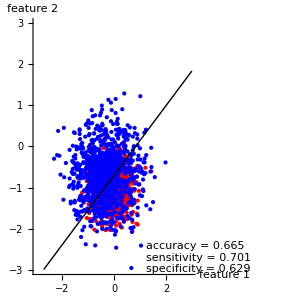
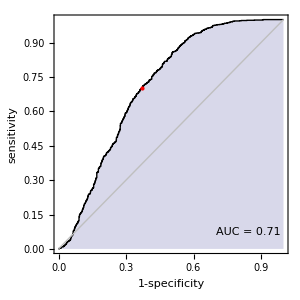
feature space and classifier | receiver operating characteristic
-Graphics- | -Graphics-

```mathematica
Block[{μp,σp,xp,xn,truth,classifier,prediction,fullroc,operatingpoint,roc,auc},
seed=3;
SeedRandom[seed];
μp=RandomReal[{-1,1},{2}];μn=RandomReal[{-1,1},{2}];
σp=RandomReal[{0.25,1}];σn=RandomReal[{0.25,1}];
xp=Map[Function[x,x+μp],RandomReal[NormalDistribution[0,σp],{1000,2}]];
xn=Map[Function[x,x+μn],RandomReal[NormalDistribution[0,σn],{1000,2}]];
truth=Join[ConstantArray[1,{1000}],ConstantArray[-1,{1000}]];

classifier=PseudoInverse[Map[Function[x,Append[x,1.]],Join[xp,xn]]].truth;

prediction=Map[Function[x,Append[x,1.]],Join[xp,xn]].classifier;

fullroc=ROC[prediction,truth];
operatingpoint=Part[fullroc,Part[Ordering[Part[fullroc,All,-1]^2],1]];
Print[fullroc,operatingpoint];
roc=Take[fullroc,All,2];auc=AUC[roc];Grid[{{Text@"feature space and classifier",Text@"receiver operating characteristic"},{ListPlot[{xp,xn},AspectRatio->1,PlotStyle->{Red,Blue},PlotRange->{{-3,3},{-3,3}},ImageSize->300,AxesLabel->{"\nfeature 1","feature 2"},Epilog->{Black,Thick,Line[endpts[classifier,3]],Text[
TableForm[{{Row[{"accuracy = ",NumberForm[ operatingpoint⟦3⟧,{4,3}]}]},{Row[{"sensitivity = ",NumberForm[ operatingpoint⟦2⟧,{4,3}]}]},{Row[{"specificity = ",NumberForm[ 1-operatingpoint⟦1⟧,{4,3}]}]}},TableAlignments->{Right}],Scaled[{0.7,0.0}],{-1,-1}]}],ListPlot[{roc,{{0,0},{1,1}}},Joined->True,Frame->True,PlotStyle->{{Thick,Black},{Thin,GrayLevel[0.75]}},FrameLabel->{"1-specificity","sensitivity",None,None},AspectRatio->1,ImageSize->300,Filling->{1->Axis},Epilog->{Red,PointSize[Large],Point[Take[operatingpoint,2]],Black,Text[Row[{"AUC = ",NumberForm[auc,{4,2}]}],{0.7,0.05},{-1,-1}]}]}}]]
```